# Projected trap analysis

## image processing

```mathematica
imagedir=".\\trap_array_images\\";
AppendTo[$Path, FileNameJoin[{NotebookDirectory[],imagedir}]];
```

## coherent 825 nm Moglabs TA

```mathematica
imagedir="trap_array_images\\coherent\\";
imagedir =FileNameJoin[{NotebookDirectory[],imagedir}];
SetDirectory[imagedir];
```

### 2D analysis - 2022.02.18

```mathematica
"20220129 trap image with TA.png.png";
```

```mathematica
img =-Graphics-;
img = ColorConvert[img,"grayscale"];
phi=-0.045;

img = ImageRotate[img,phi];
Show[img, ImageSize-> Medium]
```

-Graphics-

```mathematica
ImageData[img]//Dimensions
```

{1144,1488}

```mathematica
data = ImageData[img];
rows = data//Length;
cols= data[[1]]//Length;
data = data-data[[rows,cols]];(*subtract off the background*)
data = Replace[data,_?Negative-> 0,{2}]; 
data = data/Max[data];
```

```mathematica
y1=rows/2-155
y2 =y1+20
Show[Image[data],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{1,y1},{cols,y2}]}],ImageSize->Medium]
```

417

437

-Graphics-

```mathematica
Image[data[[rows-y2;;rows-y1, 550;; cols]]]
```

-Graphics-

{11,12,13,14}

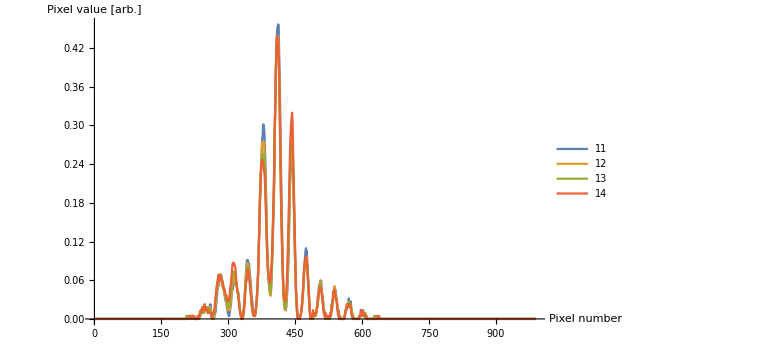

Part::take: Cannot take positions 960 through 1100 in {{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.},{8,0.},{9,0.},{10,0.},{11,0.},{12,0.},{13,0.},{14,0.167364},{15,0.171548},{16,0.171548},{17,0.171548},«18»,{36,0.171548},{37,0.179916},{38,0.1841},{39,0.192469},{40,0.188285},{41,0.1841},{42,0.192469},{43,0.188285},{44,0.1841},{45,0.1841},{46,0.188285},{47,0.188285},{48,0.188285},{49,0.188285},{50,0.188285},«785»}.

Part::take: Cannot take positions 960 through 1100 in {{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},{11.,0.},{12.,0.},{13.,0.},{14.,0.167364},«24»,{39.,0.192469},{40.,0.188285},{41.,0.1841},{42.,0.192469},{43.,0.188285},{44.,0.1841},{45.,0.1841},{46.,0.188285},{47.,0.188285},{48.,0.188285},{49.,0.188285},{50.,0.188285},«785»}.

Part::take: Cannot take positions 960 through 1100 in {{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},{11.,0.},{12.,0.},{13.,0.},{14.,0.167364},{15.,0.171548},«21»,{37.,0.179916},{38.,0.1841},{39.,0.192469},{40.,0.188285},{41.,0.1841},{42.,0.192469},{43.,0.188285},{44.,0.1841},{45.,0.1841},{46.,0.188285},{47.,0.188285},{48.,0.188285},{49.,0.188285},{50.,0.188285},«785»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

ListPlot::lpn: {{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},{11.,0.},{12.,0.},{13.,0.},{14.,0.167364},{15.,0.171548},«21»,{37.,0.179916},{38.,0.1841},{39.,0.192469},{40.,0.188285},{41.,0.1841},{42.,0.192469},{43.,0.188285},{44.,0.1841},{45.,0.1841},{46.,0.188285},{47.,0.188285},{48.,0.188285},{49.,0.188285},{50.,0.188285},«785»}⟦960;;1100⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.},{8,0.},{9,0.},{10,0.},{11,0.},{12,0.},{13,0.},{14,0.167364},{15,0.171548},{16,0.171548},{17,0.171548},{18,0.175732},{19,0.167364},{20,0.171548},{21,0.167364},{22,0.167364},{23,0.171548},{24,0.175732},{25,0.171548},{26,0.175732},{27,0.171548},{28,0.171548},{29,0.179916},{30,0.175732},{31,0.179916},{32,0.1841},{33,0.179916},{34,0.179916},{35,0.171548},{36,0.171548},{37,0.179916},{38,0.1841},{39,0.192469},{40,0.188285},{41,0.1841},{42,0.192469},{43,0.188285},{44,0.1841},{45,0.1841},{46,0.188285},{47,0.188285},{48,0.188285},{49,0.188285},{50,0.188285},{51,0.192469},{52,0.196653},{53,0.196653},{54,0.196653},{55,0.200837},{56,0.205021},{57,0.196653},{58,0.200837},{59,0.200837},{60,0.200837},{61,0.209205},{62,0.200837},{63,0.205021},{64,0.205021},{65,0.200837},{66,0.209205},{67,0.209205},{68,0.213389},{69,0.213389},{70,0.209205},{71,0.200837},{72,0.196653},{73,0.179916},{74,0.154812},{75,0.129707},{76,0.104603},{77,0.083682},{78,0.0753138},{79,0.0753138},{80,0.083682},{81,0.100418},{82,0.125523},{83,0.142259},{84,0.171548},{85,0.196653},{86,0.209205},{87,0.221757},{88,0.230126},{89,0.221757},{90,0.213389},{91,0.196653},{92,0.171548},{93,0.142259},{94,0.112971},{95,0.0962343},{96,0.0794979},{97,0.0753138},{98,0.0794979},{99,0.100418},{100,0.121339},{101,0.146444},{102,0.167364},{103,0.188285},{104,0.209205},{105,0.225941},{106,0.23431},{107,0.238494},{108,0.242678},{109,0.221757},{110,0.192469},{111,0.171548},{112,0.138075},{113,0.108787},{114,0.0878661},{115,0.083682},{116,0.083682},{117,0.0962343},{118,0.112971},{119,0.142259},{120,0.171548},{121,0.196653},{122,0.221757},{123,0.242678},{124,0.259414},{125,0.259414},{126,0.25523},{127,0.242678},{128,0.221757},{129,0.196653},{130,0.158996},{131,0.121339},{132,0.100418},{133,0.0878661},{134,0.0878661},{135,0.0962343},{136,0.121339},{137,0.146444},{138,0.175732},{139,0.205021},{140,0.238494},{141,0.25523},{142,0.271967},{143,0.288703},{144,0.284519},{145,0.267782},{146,0.242678},{147,0.213389},{148,0.175732},{149,0.142259},{150,0.117155},{151,0.0962343},{152,0.0878661},{153,0.100418},{154,0.117155},{155,0.142259},{156,0.179916},{157,0.209205},{158,0.238494},{159,0.267782},{160,0.288703},{161,0.301255},{162,0.301255},{163,0.288703},{164,0.267782},{165,0.230126},{166,0.192469},{167,0.154812},{168,0.121339},{169,0.0962343},{170,0.0878661},{171,0.0962343},{172,0.108787},{173,0.138075},{174,0.171548},{175,0.205021},{176,0.23431},{177,0.267782},{178,0.288703},{179,0.309623},{180,0.313808},{181,0.309623},{182,0.297071},{183,0.271967},{184,0.230126},{185,0.192469},{186,0.154812},{187,0.121339},{188,0.108787},{189,0.104603},{190,0.112971},{191,0.142259},{192,0.171548},{193,0.209205},{194,0.242678},{195,0.280335},{196,0.313808},{197,0.334728},{198,0.351464},{199,0.34728},{200,0.338912},{201,0.309623},{202,0.267782},{203,0.221757},{204,0.171548},{205,0.142259},{206,0.125523},{207,0.112971},{208,0.121339},{209,0.142259},{210,0.175732},{211,0.217573},{212,0.25523},{213,0.297071},{214,0.334728},{215,0.359833},{216,0.372385},{217,0.380753},{218,0.368201},{219,0.34728},{220,0.309623},{221,0.251046},{222,0.209205},{223,0.167364},{224,0.133891},{225,0.121339},{226,0.129707},{227,0.150628},{228,0.179916},{229,0.217573},{230,0.263598},{231,0.305439},{232,0.338912},{233,0.372385},{234,0.393305},{235,0.401674},{236,0.393305},{237,0.376569},{238,0.343096},{239,0.292887},{240,0.242678},{241,0.188285},{242,0.146444},{243,0.133891},{244,0.125523},{245,0.138075},{246,0.16318},{247,0.200837},{248,0.251046},{249,0.292887},{250,0.334728},{251,0.376569},{252,0.39749},{253,0.414226},{254,0.414226},{255,0.39749},{256,0.355649},{257,0.313808},{258,0.267782},{259,0.217573},{260,0.171548},{261,0.142259},{262,0.133891},{263,0.142259},{264,0.16318},{265,0.196653},{266,0.238494},{267,0.284519},{268,0.32636},{269,0.368201},{270,0.401674},{271,0.41841},{272,0.430962},{273,0.422594},{274,0.384937},{275,0.334728},{276,0.284519},{277,0.225941},{278,0.179916},{279,0.150628},{280,0.138075},{281,0.146444},{282,0.167364},{283,0.196653},{284,0.23431},{285,0.276151},{286,0.322176},{287,0.368201},{288,0.401674},{289,0.422594},{290,0.435146},{291,0.426778},{292,0.393305},{293,0.351464},{294,0.305439},{295,0.25523},{296,0.209205},{297,0.175732},{298,0.154812},{299,0.154812},{300,0.171548},{301,0.196653},{302,0.225941},{303,0.276151},{304,0.32636},{305,0.376569},{306,0.414226},{307,0.439331},{308,0.451883},{309,0.456067},{310,0.430962},{311,0.384937},{312,0.334728},{313,0.276151},{314,0.230126},{315,0.1841},{316,0.16318},{317,0.154812},{318,0.16318},{319,0.188285},{320,0.221757},{321,0.267782},{322,0.317992},{323,0.372385},{324,0.414226},{325,0.439331},{326,0.464435},{327,0.468619},{328,0.456067},{329,0.41841},{330,0.368201},{331,0.313808},{332,0.259414},{333,0.217573},{334,0.179916},{335,0.167364},{336,0.167364},{337,0.179916},{338,0.209205},{339,0.25523},{340,0.305439},{341,0.368201},{342,0.414226},{343,0.451883},{344,0.481172},{345,0.48954},{346,0.472803},{347,0.443515},{348,0.393305},{349,0.334728},{350,0.288703},{351,0.242678},{352,0.205021},{353,0.1841},{354,0.179916},{355,0.1841},{356,0.209205},{357,0.25523},{358,0.301255},{359,0.359833},{360,0.414226},{361,0.460251},{362,0.493724},{363,0.506276},{364,0.497908},{365,0.472803},{366,0.430962},{367,0.380753},{368,0.330544},{369,0.280335},{370,0.238494},{371,0.200837},{372,0.188285},{373,0.1841},{374,0.205021},{375,0.238494},{376,0.288703},{377,0.343096},{378,0.401674},{379,0.460251},{380,0.497908},{381,0.527197},{382,0.527197},{383,0.506276},{384,0.468619},{385,0.414226},{386,0.359833},{387,0.305439},{388,0.251046},{389,0.209205},{390,0.188285},{391,0.1841},{392,0.200837},{393,0.238494},{394,0.280335},{395,0.338912},{396,0.393305},{397,0.456067},{398,0.51046},{399,0.527197},{400,0.531381},{401,0.518828},{402,0.485356},{403,0.435146},{404,0.384937},{405,0.32636},{406,0.267782},{407,0.225941},{408,0.196653},{409,0.192469},{410,0.200837},{411,0.225941},{412,0.271967},{413,0.322176},{414,0.384937},{415,0.439331},{416,0.497908},{417,0.523013},{418,0.535565},{419,0.527197},{420,0.48954},{421,0.439331},{422,0.39749},{423,0.338912},{424,0.284519},{425,0.238494},{426,0.205021},{427,0.188285},{428,0.192469},{429,0.213389},{430,0.25523},{431,0.305439},{432,0.368201},{433,0.422594},{434,0.476987},{435,0.51046},{436,0.531381},{437,0.51046},{438,0.481172},{439,0.451883},{440,0.393305},{441,0.330544},{442,0.288703},{443,0.23431},{444,0.205021},{445,0.1841},{446,0.1841},{447,0.196653},{448,0.230126},{449,0.280335},{450,0.330544},{451,0.393305},{452,0.447699},{453,0.48954},{454,0.502092},{455,0.497908},{456,0.48954},{457,0.439331},{458,0.393305},{459,0.334728},{460,0.280335},{461,0.242678},{462,0.196653},{463,0.179916},{464,0.167364},{465,0.175732},{466,0.200837},{467,0.242678},{468,0.292887},{469,0.343096},{470,0.39749},{471,0.447699},{472,0.464435},{473,0.476987},{474,0.456067},{475,0.435146},{476,0.393305},{477,0.343096},{478,0.292887},{479,0.246862},{480,0.205021},{481,0.171548},{482,0.16318},{483,0.16318},{484,0.175732},{485,0.209205},{486,0.259414},{487,0.313808},{488,0.364017},{489,0.414226},{490,0.447699},{491,0.451883},{492,0.447699},{493,0.426778},{494,0.380753},{495,0.338912},{496,0.288703},{497,0.238494},{498,0.200837},{499,0.171548},{500,0.154812},{501,0.146444},{502,0.158996},{503,0.192469},{504,0.230126},{505,0.276151},{506,0.32636},{507,0.376569},{508,0.422594},{509,0.430962},{510,0.422594},{511,0.405858},{512,0.376569},{513,0.334728},{514,0.292887},{515,0.246862},{516,0.205021},{517,0.175732},{518,0.150628},{519,0.146444},{520,0.150628},{521,0.171548},{522,0.209205},{523,0.259414},{524,0.309623},{525,0.364017},{526,0.39749},{527,0.41841},{528,0.430962},{529,0.405858},{530,0.372385},{531,0.330544},{532,0.288703},{533,0.242678},{534,0.200837},{535,0.179916},{536,0.154812},{537,0.142259},{538,0.146444},{539,0.16318},{540,0.1841},{541,0.238494},{542,0.276151},{543,0.338912},{544,0.368201},{545,0.384937},{546,0.414226},{547,0.380753},{548,0.368201},{549,0.32636},{550,0.292887},{551,0.251046},{552,0.213389},{553,0.179916},{554,0.154812},{555,0.142259},{556,0.133891},{557,0.138075},{558,0.175732},{559,0.213389},{560,0.259414},{561,0.305439},{562,0.338912},{563,0.368201},{564,0.372385},{565,0.376569},{566,0.351464},{567,0.32636},{568,0.288703},{569,0.263598},{570,0.209205},{571,0.1841},{572,0.150628},{573,0.138075},{574,0.129707},{575,0.129707},{576,0.150628},{577,0.179916},{578,0.225941},{579,0.276151},{580,0.313808},{581,0.338912},{582,0.359833},{583,0.355649},{584,0.343096},{585,0.309623},{586,0.284519},{587,0.246862},{588,0.213389},{589,0.188285},{590,0.154812},{591,0.138075},{592,0.125523},{593,0.125523},{594,0.142259},{595,0.171548},{596,0.205021},{597,0.246862},{598,0.297071},{599,0.330544},{600,0.343096},{601,0.330544},{602,0.32636},{603,0.305439},{604,0.267782},{605,0.230126},{606,0.205021},{607,0.175732},{608,0.146444},{609,0.125523},{610,0.117155},{611,0.121339},{612,0.129707},{613,0.154812},{614,0.188285},{615,0.221757},{616,0.267782},{617,0.292887},{618,0.317992},{619,0.313808},{620,0.297071},{621,0.280335},{622,0.259414},{623,0.221757},{624,0.192469},{625,0.171548},{626,0.142259},{627,0.121339},{628,0.112971},{629,0.104603},{630,0.117155},{631,0.138075},{632,0.167364},{633,0.209205},{634,0.242678},{635,0.267782},{636,0.292887},{637,0.288703},{638,0.276151},{639,0.246862},{640,0.230126},{641,0.196653},{642,0.179916},{643,0.158996},{644,0.133891},{645,0.117155},{646,0.0962343},{647,0.104603},{648,0.108787},{649,0.129707},{650,0.150628},{651,0.188285},{652,0.217573},{653,0.246862},{654,0.259414},{655,0.259414},{656,0.25523},{657,0.238494},{658,0.217573},{659,0.192469},{660,0.171548},{661,0.154812},{662,0.129707},{663,0.117155},{664,0.100418},{665,0.0878661},{666,0.0962343},{667,0.100418},{668,0.129707},{669,0.154812},{670,0.192469},{671,0.225941},{672,0.242678},{673,0.25523},{674,0.251046},{675,0.238494},{676,0.225941},{677,0.209205},{678,0.175732},{679,0.158996},{680,0.133891},{681,0.112971},{682,0.0962343},{683,0.0878661},{684,0.0878661},{685,0.0962343},{686,0.117155},{687,0.142259},{688,0.16318},{689,0.192469},{690,0.213389},{691,0.225941},{692,0.230126},{693,0.213389},{694,0.205021},{695,0.188285},{696,0.16318},{697,0.146444},{698,0.129707},{699,0.112971},{700,0.100418},{701,0.0920502},{702,0.0920502},{703,0.104603},{704,0.121339},{705,0.142259},{706,0.16318},{707,0.1841},{708,0.205021},{709,0.221757},{710,0.221757},{711,0.238494},{712,0.23431},{713,0.23431},{714,0.23431},{715,0.238494},{716,0.23431},{717,0.230126},{718,0.230126},{719,0.230126},{720,0.225941},{721,0.230126},{722,0.230126},{723,0.225941},{724,0.225941},{725,0.225941},{726,0.225941},{727,0.225941},{728,0.225941},{729,0.221757},{730,0.217573},{731,0.221757},{732,0.225941},{733,0.221757},{734,0.217573},{735,0.217573},{736,0.217573},{737,0.217573},{738,0.221757},{739,0.221757},{740,0.213389},{741,0.213389},{742,0.213389},{743,0.209205},{744,0.209205},{745,0.213389},{746,0.209205},{747,0.205021},{748,0.200837},{749,0.209205},{750,0.205021},{751,0.205021},{752,0.209205},{753,0.205021},{754,0.205021},{755,0.200837},{756,0.205021},{757,0.196653},{758,0.196653},{759,0.188285},{760,0.192469},{761,0.192469},{762,0.188285},{763,0.188285},{764,0.188285},{765,0.196653},{766,0.192469},{767,0.188285},{768,0.188285},{769,0.192469},{770,0.192469},{771,0.1841},{772,0.179916},{773,0.1841},{774,0.179916},{775,0.179916},{776,0.1841},{777,0.179916},{778,0.175732},{779,0.175732},{780,0.175732},{781,0.179916},{782,0.179916},{783,0.179916},{784,0.179916},{785,0.179916},{786,0.179916},{787,0.175732},{788,0.175732},{789,0.171548},{790,0.167364},{791,0.171548},{792,0.167364},{793,0.16318},{794,0.16318},{795,0.167364},{796,0.175732},{797,0.171548},{798,0.171548},{799,0.171548},{800,0.171548},{801,0.171548},{802,0.171548},{803,0.175732},{804,0.171548},{805,0.167364},{806,0.16318},{807,0.16318},{808,0.16318},{809,0.158996},{810,0.158996},{811,0.158996},{812,0.154812},{813,0.150628},{814,0.150628},{815,0.154812},{816,0.150628},{817,0.154812},{818,0.154812},{819,0.158996},{820,0.154812},{821,0.154812},{822,0.154812},{823,0.},{824,0.},{825,0.},{826,0.},{827,0.},{828,0.},{829,0.},{830,0.},{831,0.},{832,0.},{833,0.},{834,0.},{835,0.}}⟦960;;1100⟧,Joined→True,LabelStyle→Directive[GrayLevel[0],Medium],AxesLabel→{Pixel number,Pixel value [arb.]},ImageSize→Large]

```mathematica
itable=Range[11,14];
ListPlot[Evaluate[Table[Transpose@{Range[cols-499],data[[rows-y2+i;;rows-y1+i, 500;; cols]][[1]]},{i,itable}]], Joined->True,AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Large,PlotRange->All,PlotLegends->itable]
```

```mathematica
i=13;
linedata=Transpose@{Range[cols-499],data[[rows-y2+i;;rows-y1+i, 500;; cols]][[1]]};
```

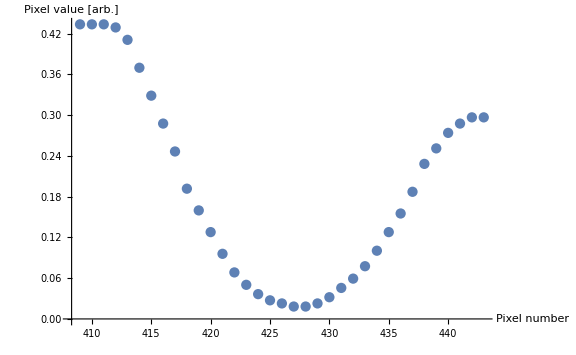

```mathematica
ListPlot[linedata[[409;;443]],Joined->False,LabelStyle->Directive[Black, Medium],AxesLabel-> {"Pixel number","Pixel value [arb.]"},ImageSize->Large,PlotRange->All]
```

```mathematica
linedata[[409;;443]]//Length
```

35

```mathematica
n=6;
model= a1 Exp[(-2(x-μx1)^2)/w1^2](1-a2 Sum[ Exp[(-2(x-μx2*j-μx1)^2)/w2^2],{j,1,n}]);
```

```mathematica
model
```

a1 ⅇ^(-(2 (x-μx1)^2)/w1^2) ∑_(j=0)^n (1-a2 ⅇ^(-(2 (x-(1+j) μx2)^2)/w2^2))

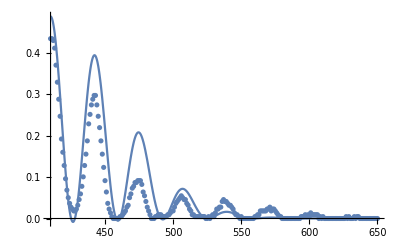

{a1→1,a2→1,μx1→410,w1→100,w2→20,μx2→33}

```mathematica
n=7;
data = linedata[[410;;650]];
model= a1 Exp[(-2(x-μx1)^2)/w1^2](1-a2 Sum[ Exp[(-2(x-μx2*(j+0.5)-μx1)^2)/w2^2],{j,-n,n}]);
params = {a1->1,a2->1,μx1->410,w1->100,w2->20,μx2->33};
Show[Plot[model/.params,{x,410,650},PlotRange->All],ListPlot[data]]
params
```

```mathematica
fit=FindFit[data,model,{{a1,0.75},{a2,1},{μx1,410},{w1,100},{μx2,33},{w2,20}},x]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a1→9.87507,a2→0.817573,μx1→410.717,w1→70.9396,μx2→32.013,w2→30.6258}

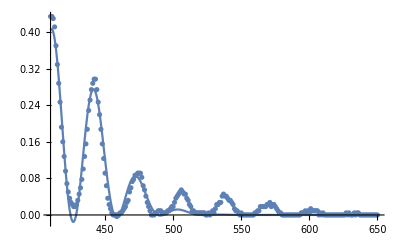

```mathematica
Show[Plot[model/.fit,{x,410,650},PlotRange->All],ListPlot[data]]
```

```mathematica
fit
```

{a1→9.87507,a2→0.817573,μx1→410.717,w1→70.9396,μx2→32.013,w2→30.6258}

Thorcam pixesl 3.45 um x 3.45

```mathematica
""
```

```mathematica
"Gaussian site waist, um"
30.6258*3.45
"Magnification error from 2022.01.08"
25.3347/30.6258
"Gaussian envelope waist, um"(*using yesterday's fit, with the magnification correction*)
160.928*3.45/(25.3347/30.6258)
```

Gaussian site waist, um

105.659

Magnification error from 2022.01.08

0.827234

Gaussian envelope waist, um

671.154

### 2D analysis - 2022.01.29

```mathematica
"20220129 trap image with TA.png.png";
```

```mathematica
img =-Graphics-;
img = ColorConvert[img,"grayscale"];
phi=-0.045;

img = ImageRotate[img,phi];
Show[img, ImageSize-> Medium]
```

-Graphics-

```mathematica
ImageData[img]//Dimensions
```

{1144,1488}

```mathematica
data = ImageData[img];
rows = data//Length;
cols= data[[1]]//Length;
data = data-data[[rows,cols]];(*subtract off the background*)
data = Replace[data,_?Negative-> 0,{2}]; 
data = data/Max[data];
```

```mathematica
y1=rows/2-155
y2 =y1+20
Show[Image[data],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{1,y1},{cols,y2}]}],ImageSize->Medium]
```

417

437

-Graphics-

```mathematica
Image[data[[rows-y2;;rows-y1, 550;; cols]]]
```

-Graphics-

```mathematica
itable=Range[11,14];
ListPlot[Evaluate[Table[Transpose@{Range[cols-499],data[[rows-y2+i;;rows-y1+i, 500;; cols]][[1]]},{i,itable}]], Joined->True,AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Large,PlotRange->All,PlotLegends->itable]
```

{11,12,13,14}

-Graphics-

Part::take: Cannot take positions 960 through 1100 in {{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.},{8,0.},{9,0.},{10,0.},{11,0.},{12,0.},{13,0.},{14,0.167364},{15,0.171548},{16,0.171548},{17,0.171548},«18»,{36,0.171548},{37,0.179916},{38,0.1841},{39,0.192469},{40,0.188285},{41,0.1841},{42,0.192469},{43,0.188285},{44,0.1841},{45,0.1841},{46,0.188285},{47,0.188285},{48,0.188285},{49,0.188285},{50,0.188285},«785»}.

Part::take: Cannot take positions 960 through 1100 in {{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},{11.,0.},{12.,0.},{13.,0.},{14.,0.167364},«24»,{39.,0.192469},{40.,0.188285},{41.,0.1841},{42.,0.192469},{43.,0.188285},{44.,0.1841},{45.,0.1841},{46.,0.188285},{47.,0.188285},{48.,0.188285},{49.,0.188285},{50.,0.188285},«785»}.

Part::take: Cannot take positions 960 through 1100 in {{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},{11.,0.},{12.,0.},{13.,0.},{14.,0.167364},{15.,0.171548},«21»,{37.,0.179916},{38.,0.1841},{39.,0.192469},{40.,0.188285},{41.,0.1841},{42.,0.192469},{43.,0.188285},{44.,0.1841},{45.,0.1841},{46.,0.188285},{47.,0.188285},{48.,0.188285},{49.,0.188285},{50.,0.188285},«785»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

ListPlot::lpn: {{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},{11.,0.},{12.,0.},{13.,0.},{14.,0.167364},{15.,0.171548},«21»,{37.,0.179916},{38.,0.1841},{39.,0.192469},{40.,0.188285},{41.,0.1841},{42.,0.192469},{43.,0.188285},{44.,0.1841},{45.,0.1841},{46.,0.188285},{47.,0.188285},{48.,0.188285},{49.,0.188285},{50.,0.188285},«785»}⟦960;;1100⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.},{8,0.},{9,0.},{10,0.},{11,0.},{12,0.},{13,0.},{14,0.167364},{15,0.171548},{16,0.171548},{17,0.171548},{18,0.175732},{19,0.167364},{20,0.171548},{21,0.167364},{22,0.167364},{23,0.171548},{24,0.175732},{25,0.171548},{26,0.175732},{27,0.171548},{28,0.171548},{29,0.179916},{30,0.175732},{31,0.179916},{32,0.1841},{33,0.179916},{34,0.179916},{35,0.171548},{36,0.171548},{37,0.179916},{38,0.1841},{39,0.192469},{40,0.188285},{41,0.1841},{42,0.192469},{43,0.188285},{44,0.1841},{45,0.1841},{46,0.188285},{47,0.188285},{48,0.188285},{49,0.188285},{50,0.188285},{51,0.192469},{52,0.196653},{53,0.196653},{54,0.196653},{55,0.200837},{56,0.205021},{57,0.196653},{58,0.200837},{59,0.200837},{60,0.200837},{61,0.209205},{62,0.200837},{63,0.205021},{64,0.205021},{65,0.200837},{66,0.209205},{67,0.209205},{68,0.213389},{69,0.213389},{70,0.209205},{71,0.200837},{72,0.196653},{73,0.179916},{74,0.154812},{75,0.129707},{76,0.104603},{77,0.083682},{78,0.0753138},{79,0.0753138},{80,0.083682},{81,0.100418},{82,0.125523},{83,0.142259},{84,0.171548},{85,0.196653},{86,0.209205},{87,0.221757},{88,0.230126},{89,0.221757},{90,0.213389},{91,0.196653},{92,0.171548},{93,0.142259},{94,0.112971},{95,0.0962343},{96,0.0794979},{97,0.0753138},{98,0.0794979},{99,0.100418},{100,0.121339},{101,0.146444},{102,0.167364},{103,0.188285},{104,0.209205},{105,0.225941},{106,0.23431},{107,0.238494},{108,0.242678},{109,0.221757},{110,0.192469},{111,0.171548},{112,0.138075},{113,0.108787},{114,0.0878661},{115,0.083682},{116,0.083682},{117,0.0962343},{118,0.112971},{119,0.142259},{120,0.171548},{121,0.196653},{122,0.221757},{123,0.242678},{124,0.259414},{125,0.259414},{126,0.25523},{127,0.242678},{128,0.221757},{129,0.196653},{130,0.158996},{131,0.121339},{132,0.100418},{133,0.0878661},{134,0.0878661},{135,0.0962343},{136,0.121339},{137,0.146444},{138,0.175732},{139,0.205021},{140,0.238494},{141,0.25523},{142,0.271967},{143,0.288703},{144,0.284519},{145,0.267782},{146,0.242678},{147,0.213389},{148,0.175732},{149,0.142259},{150,0.117155},{151,0.0962343},{152,0.0878661},{153,0.100418},{154,0.117155},{155,0.142259},{156,0.179916},{157,0.209205},{158,0.238494},{159,0.267782},{160,0.288703},{161,0.301255},{162,0.301255},{163,0.288703},{164,0.267782},{165,0.230126},{166,0.192469},{167,0.154812},{168,0.121339},{169,0.0962343},{170,0.0878661},{171,0.0962343},{172,0.108787},{173,0.138075},{174,0.171548},{175,0.205021},{176,0.23431},{177,0.267782},{178,0.288703},{179,0.309623},{180,0.313808},{181,0.309623},{182,0.297071},{183,0.271967},{184,0.230126},{185,0.192469},{186,0.154812},{187,0.121339},{188,0.108787},{189,0.104603},{190,0.112971},{191,0.142259},{192,0.171548},{193,0.209205},{194,0.242678},{195,0.280335},{196,0.313808},{197,0.334728},{198,0.351464},{199,0.34728},{200,0.338912},{201,0.309623},{202,0.267782},{203,0.221757},{204,0.171548},{205,0.142259},{206,0.125523},{207,0.112971},{208,0.121339},{209,0.142259},{210,0.175732},{211,0.217573},{212,0.25523},{213,0.297071},{214,0.334728},{215,0.359833},{216,0.372385},{217,0.380753},{218,0.368201},{219,0.34728},{220,0.309623},{221,0.251046},{222,0.209205},{223,0.167364},{224,0.133891},{225,0.121339},{226,0.129707},{227,0.150628},{228,0.179916},{229,0.217573},{230,0.263598},{231,0.305439},{232,0.338912},{233,0.372385},{234,0.393305},{235,0.401674},{236,0.393305},{237,0.376569},{238,0.343096},{239,0.292887},{240,0.242678},{241,0.188285},{242,0.146444},{243,0.133891},{244,0.125523},{245,0.138075},{246,0.16318},{247,0.200837},{248,0.251046},{249,0.292887},{250,0.334728},{251,0.376569},{252,0.39749},{253,0.414226},{254,0.414226},{255,0.39749},{256,0.355649},{257,0.313808},{258,0.267782},{259,0.217573},{260,0.171548},{261,0.142259},{262,0.133891},{263,0.142259},{264,0.16318},{265,0.196653},{266,0.238494},{267,0.284519},{268,0.32636},{269,0.368201},{270,0.401674},{271,0.41841},{272,0.430962},{273,0.422594},{274,0.384937},{275,0.334728},{276,0.284519},{277,0.225941},{278,0.179916},{279,0.150628},{280,0.138075},{281,0.146444},{282,0.167364},{283,0.196653},{284,0.23431},{285,0.276151},{286,0.322176},{287,0.368201},{288,0.401674},{289,0.422594},{290,0.435146},{291,0.426778},{292,0.393305},{293,0.351464},{294,0.305439},{295,0.25523},{296,0.209205},{297,0.175732},{298,0.154812},{299,0.154812},{300,0.171548},{301,0.196653},{302,0.225941},{303,0.276151},{304,0.32636},{305,0.376569},{306,0.414226},{307,0.439331},{308,0.451883},{309,0.456067},{310,0.430962},{311,0.384937},{312,0.334728},{313,0.276151},{314,0.230126},{315,0.1841},{316,0.16318},{317,0.154812},{318,0.16318},{319,0.188285},{320,0.221757},{321,0.267782},{322,0.317992},{323,0.372385},{324,0.414226},{325,0.439331},{326,0.464435},{327,0.468619},{328,0.456067},{329,0.41841},{330,0.368201},{331,0.313808},{332,0.259414},{333,0.217573},{334,0.179916},{335,0.167364},{336,0.167364},{337,0.179916},{338,0.209205},{339,0.25523},{340,0.305439},{341,0.368201},{342,0.414226},{343,0.451883},{344,0.481172},{345,0.48954},{346,0.472803},{347,0.443515},{348,0.393305},{349,0.334728},{350,0.288703},{351,0.242678},{352,0.205021},{353,0.1841},{354,0.179916},{355,0.1841},{356,0.209205},{357,0.25523},{358,0.301255},{359,0.359833},{360,0.414226},{361,0.460251},{362,0.493724},{363,0.506276},{364,0.497908},{365,0.472803},{366,0.430962},{367,0.380753},{368,0.330544},{369,0.280335},{370,0.238494},{371,0.200837},{372,0.188285},{373,0.1841},{374,0.205021},{375,0.238494},{376,0.288703},{377,0.343096},{378,0.401674},{379,0.460251},{380,0.497908},{381,0.527197},{382,0.527197},{383,0.506276},{384,0.468619},{385,0.414226},{386,0.359833},{387,0.305439},{388,0.251046},{389,0.209205},{390,0.188285},{391,0.1841},{392,0.200837},{393,0.238494},{394,0.280335},{395,0.338912},{396,0.393305},{397,0.456067},{398,0.51046},{399,0.527197},{400,0.531381},{401,0.518828},{402,0.485356},{403,0.435146},{404,0.384937},{405,0.32636},{406,0.267782},{407,0.225941},{408,0.196653},{409,0.192469},{410,0.200837},{411,0.225941},{412,0.271967},{413,0.322176},{414,0.384937},{415,0.439331},{416,0.497908},{417,0.523013},{418,0.535565},{419,0.527197},{420,0.48954},{421,0.439331},{422,0.39749},{423,0.338912},{424,0.284519},{425,0.238494},{426,0.205021},{427,0.188285},{428,0.192469},{429,0.213389},{430,0.25523},{431,0.305439},{432,0.368201},{433,0.422594},{434,0.476987},{435,0.51046},{436,0.531381},{437,0.51046},{438,0.481172},{439,0.451883},{440,0.393305},{441,0.330544},{442,0.288703},{443,0.23431},{444,0.205021},{445,0.1841},{446,0.1841},{447,0.196653},{448,0.230126},{449,0.280335},{450,0.330544},{451,0.393305},{452,0.447699},{453,0.48954},{454,0.502092},{455,0.497908},{456,0.48954},{457,0.439331},{458,0.393305},{459,0.334728},{460,0.280335},{461,0.242678},{462,0.196653},{463,0.179916},{464,0.167364},{465,0.175732},{466,0.200837},{467,0.242678},{468,0.292887},{469,0.343096},{470,0.39749},{471,0.447699},{472,0.464435},{473,0.476987},{474,0.456067},{475,0.435146},{476,0.393305},{477,0.343096},{478,0.292887},{479,0.246862},{480,0.205021},{481,0.171548},{482,0.16318},{483,0.16318},{484,0.175732},{485,0.209205},{486,0.259414},{487,0.313808},{488,0.364017},{489,0.414226},{490,0.447699},{491,0.451883},{492,0.447699},{493,0.426778},{494,0.380753},{495,0.338912},{496,0.288703},{497,0.238494},{498,0.200837},{499,0.171548},{500,0.154812},{501,0.146444},{502,0.158996},{503,0.192469},{504,0.230126},{505,0.276151},{506,0.32636},{507,0.376569},{508,0.422594},{509,0.430962},{510,0.422594},{511,0.405858},{512,0.376569},{513,0.334728},{514,0.292887},{515,0.246862},{516,0.205021},{517,0.175732},{518,0.150628},{519,0.146444},{520,0.150628},{521,0.171548},{522,0.209205},{523,0.259414},{524,0.309623},{525,0.364017},{526,0.39749},{527,0.41841},{528,0.430962},{529,0.405858},{530,0.372385},{531,0.330544},{532,0.288703},{533,0.242678},{534,0.200837},{535,0.179916},{536,0.154812},{537,0.142259},{538,0.146444},{539,0.16318},{540,0.1841},{541,0.238494},{542,0.276151},{543,0.338912},{544,0.368201},{545,0.384937},{546,0.414226},{547,0.380753},{548,0.368201},{549,0.32636},{550,0.292887},{551,0.251046},{552,0.213389},{553,0.179916},{554,0.154812},{555,0.142259},{556,0.133891},{557,0.138075},{558,0.175732},{559,0.213389},{560,0.259414},{561,0.305439},{562,0.338912},{563,0.368201},{564,0.372385},{565,0.376569},{566,0.351464},{567,0.32636},{568,0.288703},{569,0.263598},{570,0.209205},{571,0.1841},{572,0.150628},{573,0.138075},{574,0.129707},{575,0.129707},{576,0.150628},{577,0.179916},{578,0.225941},{579,0.276151},{580,0.313808},{581,0.338912},{582,0.359833},{583,0.355649},{584,0.343096},{585,0.309623},{586,0.284519},{587,0.246862},{588,0.213389},{589,0.188285},{590,0.154812},{591,0.138075},{592,0.125523},{593,0.125523},{594,0.142259},{595,0.171548},{596,0.205021},{597,0.246862},{598,0.297071},{599,0.330544},{600,0.343096},{601,0.330544},{602,0.32636},{603,0.305439},{604,0.267782},{605,0.230126},{606,0.205021},{607,0.175732},{608,0.146444},{609,0.125523},{610,0.117155},{611,0.121339},{612,0.129707},{613,0.154812},{614,0.188285},{615,0.221757},{616,0.267782},{617,0.292887},{618,0.317992},{619,0.313808},{620,0.297071},{621,0.280335},{622,0.259414},{623,0.221757},{624,0.192469},{625,0.171548},{626,0.142259},{627,0.121339},{628,0.112971},{629,0.104603},{630,0.117155},{631,0.138075},{632,0.167364},{633,0.209205},{634,0.242678},{635,0.267782},{636,0.292887},{637,0.288703},{638,0.276151},{639,0.246862},{640,0.230126},{641,0.196653},{642,0.179916},{643,0.158996},{644,0.133891},{645,0.117155},{646,0.0962343},{647,0.104603},{648,0.108787},{649,0.129707},{650,0.150628},{651,0.188285},{652,0.217573},{653,0.246862},{654,0.259414},{655,0.259414},{656,0.25523},{657,0.238494},{658,0.217573},{659,0.192469},{660,0.171548},{661,0.154812},{662,0.129707},{663,0.117155},{664,0.100418},{665,0.0878661},{666,0.0962343},{667,0.100418},{668,0.129707},{669,0.154812},{670,0.192469},{671,0.225941},{672,0.242678},{673,0.25523},{674,0.251046},{675,0.238494},{676,0.225941},{677,0.209205},{678,0.175732},{679,0.158996},{680,0.133891},{681,0.112971},{682,0.0962343},{683,0.0878661},{684,0.0878661},{685,0.0962343},{686,0.117155},{687,0.142259},{688,0.16318},{689,0.192469},{690,0.213389},{691,0.225941},{692,0.230126},{693,0.213389},{694,0.205021},{695,0.188285},{696,0.16318},{697,0.146444},{698,0.129707},{699,0.112971},{700,0.100418},{701,0.0920502},{702,0.0920502},{703,0.104603},{704,0.121339},{705,0.142259},{706,0.16318},{707,0.1841},{708,0.205021},{709,0.221757},{710,0.221757},{711,0.238494},{712,0.23431},{713,0.23431},{714,0.23431},{715,0.238494},{716,0.23431},{717,0.230126},{718,0.230126},{719,0.230126},{720,0.225941},{721,0.230126},{722,0.230126},{723,0.225941},{724,0.225941},{725,0.225941},{726,0.225941},{727,0.225941},{728,0.225941},{729,0.221757},{730,0.217573},{731,0.221757},{732,0.225941},{733,0.221757},{734,0.217573},{735,0.217573},{736,0.217573},{737,0.217573},{738,0.221757},{739,0.221757},{740,0.213389},{741,0.213389},{742,0.213389},{743,0.209205},{744,0.209205},{745,0.213389},{746,0.209205},{747,0.205021},{748,0.200837},{749,0.209205},{750,0.205021},{751,0.205021},{752,0.209205},{753,0.205021},{754,0.205021},{755,0.200837},{756,0.205021},{757,0.196653},{758,0.196653},{759,0.188285},{760,0.192469},{761,0.192469},{762,0.188285},{763,0.188285},{764,0.188285},{765,0.196653},{766,0.192469},{767,0.188285},{768,0.188285},{769,0.192469},{770,0.192469},{771,0.1841},{772,0.179916},{773,0.1841},{774,0.179916},{775,0.179916},{776,0.1841},{777,0.179916},{778,0.175732},{779,0.175732},{780,0.175732},{781,0.179916},{782,0.179916},{783,0.179916},{784,0.179916},{785,0.179916},{786,0.179916},{787,0.175732},{788,0.175732},{789,0.171548},{790,0.167364},{791,0.171548},{792,0.167364},{793,0.16318},{794,0.16318},{795,0.167364},{796,0.175732},{797,0.171548},{798,0.171548},{799,0.171548},{800,0.171548},{801,0.171548},{802,0.171548},{803,0.175732},{804,0.171548},{805,0.167364},{806,0.16318},{807,0.16318},{808,0.16318},{809,0.158996},{810,0.158996},{811,0.158996},{812,0.154812},{813,0.150628},{814,0.150628},{815,0.154812},{816,0.150628},{817,0.154812},{818,0.154812},{819,0.158996},{820,0.154812},{821,0.154812},{822,0.154812},{823,0.},{824,0.},{825,0.},{826,0.},{827,0.},{828,0.},{829,0.},{830,0.},{831,0.},{832,0.},{833,0.},{834,0.},{835,0.}}⟦960;;1100⟧,Joined→True,LabelStyle→Directive[GrayLevel[0],Medium],AxesLabel→{Pixel number,Pixel value [arb.]},ImageSize→Large]

```mathematica
i=13;
linedata=Transpose@{Range[cols-499],data[[rows-y2+i;;rows-y1+i, 500;; cols]][[1]]};
```

```mathematica
ListPlot[linedata[[409;;443]],Joined->False,LabelStyle->Directive[Black, Medium],AxesLabel-> {"Pixel number","Pixel value [arb.]"},ImageSize->Large,PlotRange->All]
```

-Graphics-

```mathematica
linedata[[409;;443]]//Length
```

35

```mathematica
n=6;
model= a1 Exp[(-2(x-μx1)^2)/w1^2](1-a2 Sum[ Exp[(-2(x-μx2*j-μx1)^2)/w2^2],{j,1,n}]);
```

```mathematica
model
```

a1 ⅇ^(-(2 (x-μx1)^2)/w1^2) ∑_(j=0)^n (1-a2 ⅇ^(-(2 (x-(1+j) μx2)^2)/w2^2))

```mathematica
n=7;
data = linedata[[410;;650]];
model= a1 Exp[(-2(x-μx1)^2)/w1^2](1-a2 Sum[ Exp[(-2(x-μx2*(j+0.5)-μx1)^2)/w2^2],{j,-n,n}]);
params = {a1->1,a2->1,μx1->410,w1->100,w2->20,μx2->33};
Show[Plot[model/.params,{x,410,650},PlotRange->All],ListPlot[data]]
params
```

-Graphics-

{a1→1,a2→1,μx1→410,w1→100,w2→20,μx2→33}

```mathematica
fit=FindFit[data,model,{{a1,0.75},{a2,1},{μx1,410},{w1,100},{μx2,33},{w2,20}},x]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a1→9.87507,a2→0.817573,μx1→410.717,w1→70.9396,μx2→32.013,w2→30.6258}

```mathematica
Show[Plot[model/.fit,{x,410,650},PlotRange->All],ListPlot[data]]
```

-Graphics-

```mathematica
fit
```

{a1→9.87507,a2→0.817573,μx1→410.717,w1→70.9396,μx2→32.013,w2→30.6258}

Thorcam pixesl 3.45 um x 3.45

```mathematica
""
```

```mathematica
"Gaussian site waist, um"
30.6258*3.45
"Magnification error from 2022.01.08"
25.3347/30.6258
"Gaussian envelope waist, um"(*using yesterday's fit, with the magnification correction*)
160.928*3.45/(25.3347/30.6258)
```

Gaussian site waist, um

105.659

Magnification error from 2022.01.08

0.827234

Gaussian envelope waist, um

671.154

### 2D analysis - 2022.01.28

```mathematica
"20220128 trap image with TA.png.png";
```

```mathematica
img = -Graphics-;
img = ColorConvert[img,"grayscale"];
phi=-0.045;

img = ImageRotate[img,phi];
Show[img, ImageSize-> Medium]
```

-Graphics-

```mathematica
ImageData[img]//Dimensions
```

{1144,1488}

```mathematica
data = ImageData[img];
rows = data//Length;
cols= data[[1]]//Length;
data = data-data[[rows,cols]];(*subtract off the background*)
data = Replace[data,_?Negative-> 0,{2}]; 
data = data/Max[data];
```

```mathematica
y1=rows/2-60
y2 =y1+20
Show[Image[data],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{1,y1},{cols,y2}]}],ImageSize->Medium]
```

512

532

-Graphics-

```mathematica
Image[data[[rows-y2;;rows-y1, 550;; cols]]]
```

-Graphics-

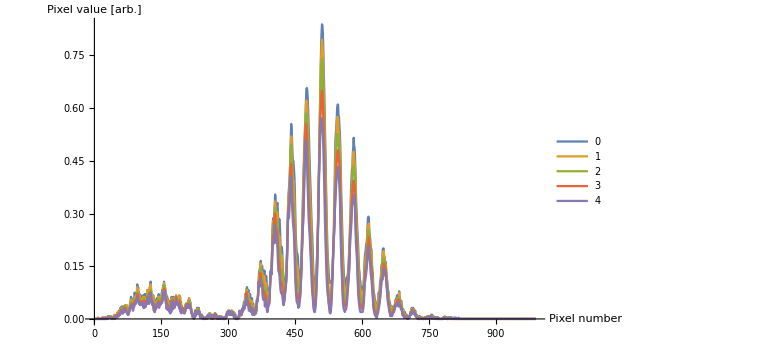

Part::take: Cannot take positions 960 through 1100 in {{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.},{8,0.},{9,0.},{10,0.},{11,0.},{12,0.},{13,0.},{14,0.167364},{15,0.171548},{16,0.171548},{17,0.171548},«18»,{36,0.171548},{37,0.179916},{38,0.1841},{39,0.192469},{40,0.188285},{41,0.1841},{42,0.192469},{43,0.188285},{44,0.1841},{45,0.1841},{46,0.188285},{47,0.188285},{48,0.188285},{49,0.188285},{50,0.188285},«785»}.

Part::take: Cannot take positions 960 through 1100 in {{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},{11.,0.},{12.,0.},{13.,0.},{14.,0.167364},«24»,{39.,0.192469},{40.,0.188285},{41.,0.1841},{42.,0.192469},{43.,0.188285},{44.,0.1841},{45.,0.1841},{46.,0.188285},{47.,0.188285},{48.,0.188285},{49.,0.188285},{50.,0.188285},«785»}.

Part::take: Cannot take positions 960 through 1100 in {{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},{11.,0.},{12.,0.},{13.,0.},{14.,0.167364},{15.,0.171548},«21»,{37.,0.179916},{38.,0.1841},{39.,0.192469},{40.,0.188285},{41.,0.1841},{42.,0.192469},{43.,0.188285},{44.,0.1841},{45.,0.1841},{46.,0.188285},{47.,0.188285},{48.,0.188285},{49.,0.188285},{50.,0.188285},«785»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

ListPlot::lpn: {{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},{11.,0.},{12.,0.},{13.,0.},{14.,0.167364},{15.,0.171548},«21»,{37.,0.179916},{38.,0.1841},{39.,0.192469},{40.,0.188285},{41.,0.1841},{42.,0.192469},{43.,0.188285},{44.,0.1841},{45.,0.1841},{46.,0.188285},{47.,0.188285},{48.,0.188285},{49.,0.188285},{50.,0.188285},«785»}⟦960;;1100⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.},{8,0.},{9,0.},{10,0.},{11,0.},{12,0.},{13,0.},{14,0.167364},{15,0.171548},{16,0.171548},{17,0.171548},{18,0.175732},{19,0.167364},{20,0.171548},{21,0.167364},{22,0.167364},{23,0.171548},{24,0.175732},{25,0.171548},{26,0.175732},{27,0.171548},{28,0.171548},{29,0.179916},{30,0.175732},{31,0.179916},{32,0.1841},{33,0.179916},{34,0.179916},{35,0.171548},{36,0.171548},{37,0.179916},{38,0.1841},{39,0.192469},{40,0.188285},{41,0.1841},{42,0.192469},{43,0.188285},{44,0.1841},{45,0.1841},{46,0.188285},{47,0.188285},{48,0.188285},{49,0.188285},{50,0.188285},{51,0.192469},{52,0.196653},{53,0.196653},{54,0.196653},{55,0.200837},{56,0.205021},{57,0.196653},{58,0.200837},{59,0.200837},{60,0.200837},{61,0.209205},{62,0.200837},{63,0.205021},{64,0.205021},{65,0.200837},{66,0.209205},{67,0.209205},{68,0.213389},{69,0.213389},{70,0.209205},{71,0.200837},{72,0.196653},{73,0.179916},{74,0.154812},{75,0.129707},{76,0.104603},{77,0.083682},{78,0.0753138},{79,0.0753138},{80,0.083682},{81,0.100418},{82,0.125523},{83,0.142259},{84,0.171548},{85,0.196653},{86,0.209205},{87,0.221757},{88,0.230126},{89,0.221757},{90,0.213389},{91,0.196653},{92,0.171548},{93,0.142259},{94,0.112971},{95,0.0962343},{96,0.0794979},{97,0.0753138},{98,0.0794979},{99,0.100418},{100,0.121339},{101,0.146444},{102,0.167364},{103,0.188285},{104,0.209205},{105,0.225941},{106,0.23431},{107,0.238494},{108,0.242678},{109,0.221757},{110,0.192469},{111,0.171548},{112,0.138075},{113,0.108787},{114,0.0878661},{115,0.083682},{116,0.083682},{117,0.0962343},{118,0.112971},{119,0.142259},{120,0.171548},{121,0.196653},{122,0.221757},{123,0.242678},{124,0.259414},{125,0.259414},{126,0.25523},{127,0.242678},{128,0.221757},{129,0.196653},{130,0.158996},{131,0.121339},{132,0.100418},{133,0.0878661},{134,0.0878661},{135,0.0962343},{136,0.121339},{137,0.146444},{138,0.175732},{139,0.205021},{140,0.238494},{141,0.25523},{142,0.271967},{143,0.288703},{144,0.284519},{145,0.267782},{146,0.242678},{147,0.213389},{148,0.175732},{149,0.142259},{150,0.117155},{151,0.0962343},{152,0.0878661},{153,0.100418},{154,0.117155},{155,0.142259},{156,0.179916},{157,0.209205},{158,0.238494},{159,0.267782},{160,0.288703},{161,0.301255},{162,0.301255},{163,0.288703},{164,0.267782},{165,0.230126},{166,0.192469},{167,0.154812},{168,0.121339},{169,0.0962343},{170,0.0878661},{171,0.0962343},{172,0.108787},{173,0.138075},{174,0.171548},{175,0.205021},{176,0.23431},{177,0.267782},{178,0.288703},{179,0.309623},{180,0.313808},{181,0.309623},{182,0.297071},{183,0.271967},{184,0.230126},{185,0.192469},{186,0.154812},{187,0.121339},{188,0.108787},{189,0.104603},{190,0.112971},{191,0.142259},{192,0.171548},{193,0.209205},{194,0.242678},{195,0.280335},{196,0.313808},{197,0.334728},{198,0.351464},{199,0.34728},{200,0.338912},{201,0.309623},{202,0.267782},{203,0.221757},{204,0.171548},{205,0.142259},{206,0.125523},{207,0.112971},{208,0.121339},{209,0.142259},{210,0.175732},{211,0.217573},{212,0.25523},{213,0.297071},{214,0.334728},{215,0.359833},{216,0.372385},{217,0.380753},{218,0.368201},{219,0.34728},{220,0.309623},{221,0.251046},{222,0.209205},{223,0.167364},{224,0.133891},{225,0.121339},{226,0.129707},{227,0.150628},{228,0.179916},{229,0.217573},{230,0.263598},{231,0.305439},{232,0.338912},{233,0.372385},{234,0.393305},{235,0.401674},{236,0.393305},{237,0.376569},{238,0.343096},{239,0.292887},{240,0.242678},{241,0.188285},{242,0.146444},{243,0.133891},{244,0.125523},{245,0.138075},{246,0.16318},{247,0.200837},{248,0.251046},{249,0.292887},{250,0.334728},{251,0.376569},{252,0.39749},{253,0.414226},{254,0.414226},{255,0.39749},{256,0.355649},{257,0.313808},{258,0.267782},{259,0.217573},{260,0.171548},{261,0.142259},{262,0.133891},{263,0.142259},{264,0.16318},{265,0.196653},{266,0.238494},{267,0.284519},{268,0.32636},{269,0.368201},{270,0.401674},{271,0.41841},{272,0.430962},{273,0.422594},{274,0.384937},{275,0.334728},{276,0.284519},{277,0.225941},{278,0.179916},{279,0.150628},{280,0.138075},{281,0.146444},{282,0.167364},{283,0.196653},{284,0.23431},{285,0.276151},{286,0.322176},{287,0.368201},{288,0.401674},{289,0.422594},{290,0.435146},{291,0.426778},{292,0.393305},{293,0.351464},{294,0.305439},{295,0.25523},{296,0.209205},{297,0.175732},{298,0.154812},{299,0.154812},{300,0.171548},{301,0.196653},{302,0.225941},{303,0.276151},{304,0.32636},{305,0.376569},{306,0.414226},{307,0.439331},{308,0.451883},{309,0.456067},{310,0.430962},{311,0.384937},{312,0.334728},{313,0.276151},{314,0.230126},{315,0.1841},{316,0.16318},{317,0.154812},{318,0.16318},{319,0.188285},{320,0.221757},{321,0.267782},{322,0.317992},{323,0.372385},{324,0.414226},{325,0.439331},{326,0.464435},{327,0.468619},{328,0.456067},{329,0.41841},{330,0.368201},{331,0.313808},{332,0.259414},{333,0.217573},{334,0.179916},{335,0.167364},{336,0.167364},{337,0.179916},{338,0.209205},{339,0.25523},{340,0.305439},{341,0.368201},{342,0.414226},{343,0.451883},{344,0.481172},{345,0.48954},{346,0.472803},{347,0.443515},{348,0.393305},{349,0.334728},{350,0.288703},{351,0.242678},{352,0.205021},{353,0.1841},{354,0.179916},{355,0.1841},{356,0.209205},{357,0.25523},{358,0.301255},{359,0.359833},{360,0.414226},{361,0.460251},{362,0.493724},{363,0.506276},{364,0.497908},{365,0.472803},{366,0.430962},{367,0.380753},{368,0.330544},{369,0.280335},{370,0.238494},{371,0.200837},{372,0.188285},{373,0.1841},{374,0.205021},{375,0.238494},{376,0.288703},{377,0.343096},{378,0.401674},{379,0.460251},{380,0.497908},{381,0.527197},{382,0.527197},{383,0.506276},{384,0.468619},{385,0.414226},{386,0.359833},{387,0.305439},{388,0.251046},{389,0.209205},{390,0.188285},{391,0.1841},{392,0.200837},{393,0.238494},{394,0.280335},{395,0.338912},{396,0.393305},{397,0.456067},{398,0.51046},{399,0.527197},{400,0.531381},{401,0.518828},{402,0.485356},{403,0.435146},{404,0.384937},{405,0.32636},{406,0.267782},{407,0.225941},{408,0.196653},{409,0.192469},{410,0.200837},{411,0.225941},{412,0.271967},{413,0.322176},{414,0.384937},{415,0.439331},{416,0.497908},{417,0.523013},{418,0.535565},{419,0.527197},{420,0.48954},{421,0.439331},{422,0.39749},{423,0.338912},{424,0.284519},{425,0.238494},{426,0.205021},{427,0.188285},{428,0.192469},{429,0.213389},{430,0.25523},{431,0.305439},{432,0.368201},{433,0.422594},{434,0.476987},{435,0.51046},{436,0.531381},{437,0.51046},{438,0.481172},{439,0.451883},{440,0.393305},{441,0.330544},{442,0.288703},{443,0.23431},{444,0.205021},{445,0.1841},{446,0.1841},{447,0.196653},{448,0.230126},{449,0.280335},{450,0.330544},{451,0.393305},{452,0.447699},{453,0.48954},{454,0.502092},{455,0.497908},{456,0.48954},{457,0.439331},{458,0.393305},{459,0.334728},{460,0.280335},{461,0.242678},{462,0.196653},{463,0.179916},{464,0.167364},{465,0.175732},{466,0.200837},{467,0.242678},{468,0.292887},{469,0.343096},{470,0.39749},{471,0.447699},{472,0.464435},{473,0.476987},{474,0.456067},{475,0.435146},{476,0.393305},{477,0.343096},{478,0.292887},{479,0.246862},{480,0.205021},{481,0.171548},{482,0.16318},{483,0.16318},{484,0.175732},{485,0.209205},{486,0.259414},{487,0.313808},{488,0.364017},{489,0.414226},{490,0.447699},{491,0.451883},{492,0.447699},{493,0.426778},{494,0.380753},{495,0.338912},{496,0.288703},{497,0.238494},{498,0.200837},{499,0.171548},{500,0.154812},{501,0.146444},{502,0.158996},{503,0.192469},{504,0.230126},{505,0.276151},{506,0.32636},{507,0.376569},{508,0.422594},{509,0.430962},{510,0.422594},{511,0.405858},{512,0.376569},{513,0.334728},{514,0.292887},{515,0.246862},{516,0.205021},{517,0.175732},{518,0.150628},{519,0.146444},{520,0.150628},{521,0.171548},{522,0.209205},{523,0.259414},{524,0.309623},{525,0.364017},{526,0.39749},{527,0.41841},{528,0.430962},{529,0.405858},{530,0.372385},{531,0.330544},{532,0.288703},{533,0.242678},{534,0.200837},{535,0.179916},{536,0.154812},{537,0.142259},{538,0.146444},{539,0.16318},{540,0.1841},{541,0.238494},{542,0.276151},{543,0.338912},{544,0.368201},{545,0.384937},{546,0.414226},{547,0.380753},{548,0.368201},{549,0.32636},{550,0.292887},{551,0.251046},{552,0.213389},{553,0.179916},{554,0.154812},{555,0.142259},{556,0.133891},{557,0.138075},{558,0.175732},{559,0.213389},{560,0.259414},{561,0.305439},{562,0.338912},{563,0.368201},{564,0.372385},{565,0.376569},{566,0.351464},{567,0.32636},{568,0.288703},{569,0.263598},{570,0.209205},{571,0.1841},{572,0.150628},{573,0.138075},{574,0.129707},{575,0.129707},{576,0.150628},{577,0.179916},{578,0.225941},{579,0.276151},{580,0.313808},{581,0.338912},{582,0.359833},{583,0.355649},{584,0.343096},{585,0.309623},{586,0.284519},{587,0.246862},{588,0.213389},{589,0.188285},{590,0.154812},{591,0.138075},{592,0.125523},{593,0.125523},{594,0.142259},{595,0.171548},{596,0.205021},{597,0.246862},{598,0.297071},{599,0.330544},{600,0.343096},{601,0.330544},{602,0.32636},{603,0.305439},{604,0.267782},{605,0.230126},{606,0.205021},{607,0.175732},{608,0.146444},{609,0.125523},{610,0.117155},{611,0.121339},{612,0.129707},{613,0.154812},{614,0.188285},{615,0.221757},{616,0.267782},{617,0.292887},{618,0.317992},{619,0.313808},{620,0.297071},{621,0.280335},{622,0.259414},{623,0.221757},{624,0.192469},{625,0.171548},{626,0.142259},{627,0.121339},{628,0.112971},{629,0.104603},{630,0.117155},{631,0.138075},{632,0.167364},{633,0.209205},{634,0.242678},{635,0.267782},{636,0.292887},{637,0.288703},{638,0.276151},{639,0.246862},{640,0.230126},{641,0.196653},{642,0.179916},{643,0.158996},{644,0.133891},{645,0.117155},{646,0.0962343},{647,0.104603},{648,0.108787},{649,0.129707},{650,0.150628},{651,0.188285},{652,0.217573},{653,0.246862},{654,0.259414},{655,0.259414},{656,0.25523},{657,0.238494},{658,0.217573},{659,0.192469},{660,0.171548},{661,0.154812},{662,0.129707},{663,0.117155},{664,0.100418},{665,0.0878661},{666,0.0962343},{667,0.100418},{668,0.129707},{669,0.154812},{670,0.192469},{671,0.225941},{672,0.242678},{673,0.25523},{674,0.251046},{675,0.238494},{676,0.225941},{677,0.209205},{678,0.175732},{679,0.158996},{680,0.133891},{681,0.112971},{682,0.0962343},{683,0.0878661},{684,0.0878661},{685,0.0962343},{686,0.117155},{687,0.142259},{688,0.16318},{689,0.192469},{690,0.213389},{691,0.225941},{692,0.230126},{693,0.213389},{694,0.205021},{695,0.188285},{696,0.16318},{697,0.146444},{698,0.129707},{699,0.112971},{700,0.100418},{701,0.0920502},{702,0.0920502},{703,0.104603},{704,0.121339},{705,0.142259},{706,0.16318},{707,0.1841},{708,0.205021},{709,0.221757},{710,0.221757},{711,0.238494},{712,0.23431},{713,0.23431},{714,0.23431},{715,0.238494},{716,0.23431},{717,0.230126},{718,0.230126},{719,0.230126},{720,0.225941},{721,0.230126},{722,0.230126},{723,0.225941},{724,0.225941},{725,0.225941},{726,0.225941},{727,0.225941},{728,0.225941},{729,0.221757},{730,0.217573},{731,0.221757},{732,0.225941},{733,0.221757},{734,0.217573},{735,0.217573},{736,0.217573},{737,0.217573},{738,0.221757},{739,0.221757},{740,0.213389},{741,0.213389},{742,0.213389},{743,0.209205},{744,0.209205},{745,0.213389},{746,0.209205},{747,0.205021},{748,0.200837},{749,0.209205},{750,0.205021},{751,0.205021},{752,0.209205},{753,0.205021},{754,0.205021},{755,0.200837},{756,0.205021},{757,0.196653},{758,0.196653},{759,0.188285},{760,0.192469},{761,0.192469},{762,0.188285},{763,0.188285},{764,0.188285},{765,0.196653},{766,0.192469},{767,0.188285},{768,0.188285},{769,0.192469},{770,0.192469},{771,0.1841},{772,0.179916},{773,0.1841},{774,0.179916},{775,0.179916},{776,0.1841},{777,0.179916},{778,0.175732},{779,0.175732},{780,0.175732},{781,0.179916},{782,0.179916},{783,0.179916},{784,0.179916},{785,0.179916},{786,0.179916},{787,0.175732},{788,0.175732},{789,0.171548},{790,0.167364},{791,0.171548},{792,0.167364},{793,0.16318},{794,0.16318},{795,0.167364},{796,0.175732},{797,0.171548},{798,0.171548},{799,0.171548},{800,0.171548},{801,0.171548},{802,0.171548},{803,0.175732},{804,0.171548},{805,0.167364},{806,0.16318},{807,0.16318},{808,0.16318},{809,0.158996},{810,0.158996},{811,0.158996},{812,0.154812},{813,0.150628},{814,0.150628},{815,0.154812},{816,0.150628},{817,0.154812},{818,0.154812},{819,0.158996},{820,0.154812},{821,0.154812},{822,0.154812},{823,0.},{824,0.},{825,0.},{826,0.},{827,0.},{828,0.},{829,0.},{830,0.},{831,0.},{832,0.},{833,0.},{834,0.},{835,0.}}⟦960;;1100⟧,Joined→True,LabelStyle→Directive[GrayLevel[0],Medium],AxesLabel→{Pixel number,Pixel value [arb.]},ImageSize→Large]

```mathematica
ListPlot[Evaluate[Table[Transpose@{Range[cols-499],data[[rows-y2+i;;rows-y1+i, 500;; cols]][[1]]},{i,Range[0,4]}]], Joined->True,AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Large,PlotRange->All,PlotLegends->Range[0,4]]
```

```mathematica
i=4;
linedata=Transpose@{Range[cols-499],data[[rows-y2+i;;rows-y1+i, 500;; cols]][[1]]};
```

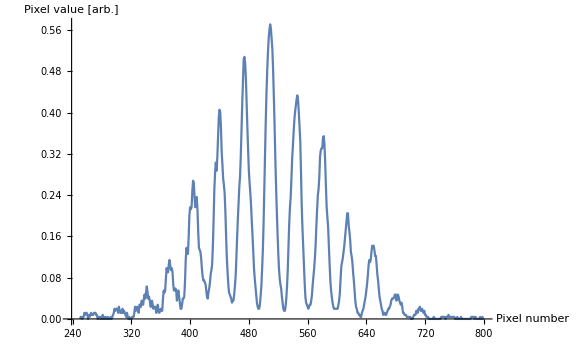

```mathematica
ListPlot[linedata[[250;;800]],Joined->True,LabelStyle->Directive[Black, Medium],AxesLabel-> {"Pixel number","Pixel value [arb.]"},ImageSize->Large]
```

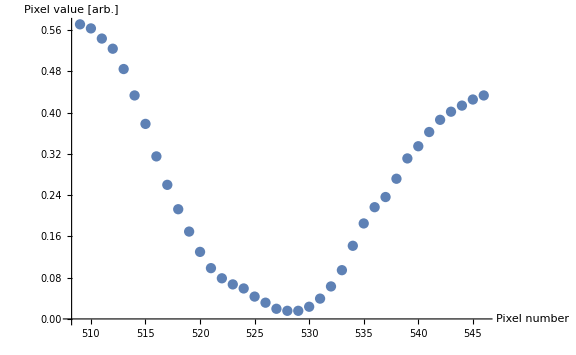

```mathematica
ListPlot[linedata[[509;;546]],Joined->False,LabelStyle->Directive[Black, Medium],AxesLabel-> {"Pixel number","Pixel value [arb.]"},ImageSize->Large,PlotRange->All]
```

```mathematica
linedata[[509;;546]]//Length
```

38

```mathematica
n=5;
model= a1 Exp[(-2(x-μx1)^2)/w1^2](1-a2 Sum[ Exp[(-2(x-μx2*j-μx1)^2)/w2^2],{j,-n,n}]);
```

```mathematica
model
```

a1 ⅇ^(-(2 (x-μx1)^2)/w1^2) ∑_(j=0)^n (1-a2 ⅇ^(-(2 (x-(1+j) μx2)^2)/w2^2))

General::munfl: Exp[-799.955] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1012.45] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1249.94] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

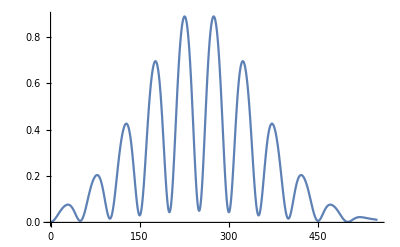

```mathematica
Plot[Exp[(-2(x-250)^2)/200^2](1-0.95Sum[Exp[(-2 (x-50*i-250)^2)/20^2],{i,-5,5}]),{x,0,550},PlotRange->All]
```

General::munfl: Exp[-1249.94] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1012.45] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-799.955] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

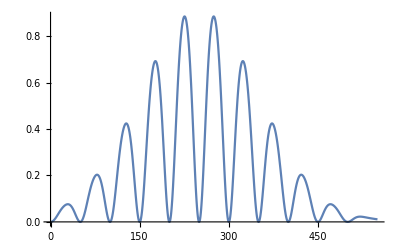

```mathematica
Plot[model/.{a1->1,a2->1,μx1->250,w1->200,w2->20,μx2->50},{x,0,550},PlotRange->All]
```

General::munfl: Exp[-1364.97] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1188.23] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1023.73] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

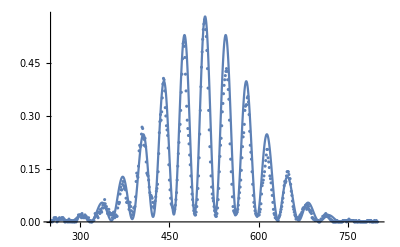

```mathematica
n=7;
model= a1 Exp[(-2(x-μx1)^2)/w1^2](1-a2 Sum[ Exp[(-2(x-μx2*(j+0.5)-μx1)^2)/w2^2],{j,-n,n}]);
Show[Plot[model/.{a1->1,a2->0.97,μx1->510,w1->160,w2->20,μx2->35},{x,250,800},PlotRange->All],ListPlot[linedata[[250;;800]]]]
```

```mathematica
{a1->1,a2->0.96,μx1->510,w1->160,w2->20,μx2->35}
```

```mathematica
fit=FindFit[linedata[[250;;800]],model,{{a1,1},{a2,0.97},{μx1,510},{w1,160},{μx2,35},{w2,20}},x]
```

{a1→1.86442,a2→0.956375,μx1→509.5,w1→160.928,μx2→35.0753,w2→25.3347}

General::munfl: Exp[-850.867] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-740.475] is too small to represent as a normalized machine number; precision may be lost.

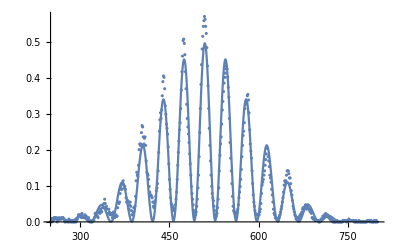

```mathematica
Show[Plot[model/.fit,{x,250,800},PlotRange->All],ListPlot[linedata[[250;;800]]]]
```

```mathematica
fit
```

{a1→1.86442,a2→0.956375,μx1→509.5,w1→160.928,μx2→35.0753,w2→25.3347}

Thorcam pixesl 3.45 um x 3.45

```mathematica
""
```

```mathematica
"Gaussian site waist, um"
25.3347*3.45
"Site to site spacing, um"
35.0753*3.45
"Gaussian envelope waist, um"
160.928*3.45
```

Gaussian site waist, um

87.4047

Site to site spacing, um

121.01

Gaussian envelope waist, um

555.202

```mathematica
model = A (1-   Exp[(-((x-μx)^2+(y-μy)^2))/σ^2])
fit =FindFit[site,model,{μx,μy,σ,A},{x,y}]
```

```mathematica
model = A (1-   Exp[(-2(x-μ)^2)/σ^2]);
fit =FindFit[linedata[[979;;1021]],model,{{μ,1000},σ,A, {b,0.5}},x]
Show[Plot[model/.fit,{x,985,1015}],ListPlot[linedata[[985;;1015]]],AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Medium]
pixel = 1.12; (*μm*)
StringForm["real space waist `` [μm]",Values[fit[[2]]]*pixel]
```

{μ→999.981,σ→10.6518,A→0.561076,b→0.5}

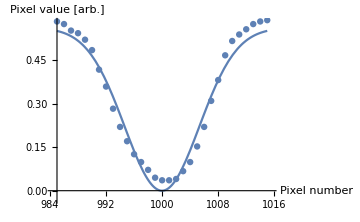

real space waist 11.93 [μm]

## 808nm 35W Aerodiode laser

### 2D analysis - 2022.02.18

```mathematica
"20220218 trap image with 808.png";
```

```mathematica
img =-Graphics-;
img = ColorConvert[img,"grayscale"];
phi=-0.07;

img = ImageRotate[img,phi];
Show[img, ImageSize-> Medium]
```

-Graphics-

```mathematica
ImageData[img]//Dimensions
```

{1144,1488}

```mathematica
data = ImageData[img];
rows = data//Length;
cols= data[[1]]//Length;
data = data-data[[rows,cols]];(*subtract off the background*)
data = Replace[data,_?Negative-> 0,{2}]; 
data = data/Max[data];
```

```mathematica
y1=(rows+1)/2-6
y2 =y1+20
Show[Image[data],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{1,y1},{cols,y2}]}],ImageSize->Medium]
```

584

604

-Graphics-

```mathematica
Image[data[[rows-y2;;rows-y1, 1;; cols]]]
```

-Graphics-

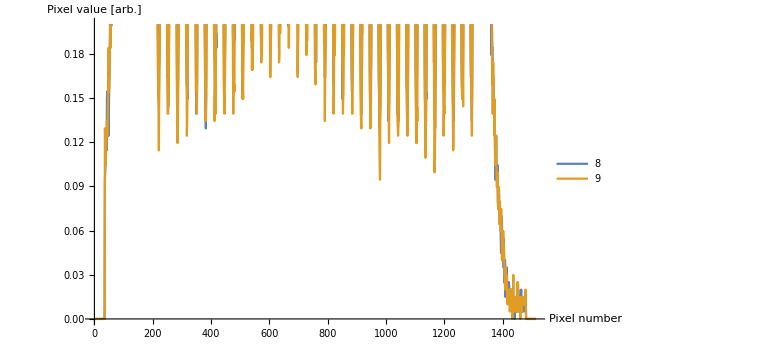

```mathematica
itable=Range[8,9];
ListPlot[Evaluate[Table[Transpose@{Range[cols],data[[rows-y2+i;;rows-y1+i, 1;; cols]][[1]]},{i,itable}]], Joined->True,AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Large,PlotRange->{0,0.2},PlotLegends->itable]
```

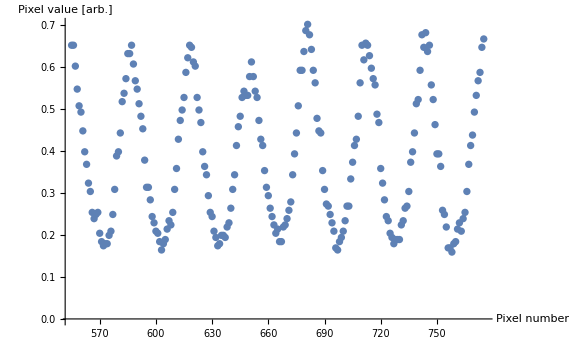

```mathematica
i=9;
dx=200;
xi=755-dx;
xf=975-dx;
linedata=Transpose@{Range[xi,xf],data[[rows-y2+i;;rows-y1+i, xi;;xf]][[1]]};
ListPlot[linedata,Joined->False,LabelStyle->Directive[Black, Medium],AxesLabel-> {"Pixel number","Pixel value [arb.]"},ImageSize->Large,PlotRange->All]
```

```mathematica
linedata[[409;;443]]//Length
```

35

```mathematica
n=7;
model= a1 Exp[(-2(x-μx1)^2)/w1^2](1-a2 Sum[ Exp[(-2(x-μx2*j-μx1)^2)/w2^2],{j,1,n}]);
```

```mathematica
model
```

a1 ⅇ^(-(2 (x-μx1)^2)/w1^2) ∑_(j=0)^n (1-a2 ⅇ^(-(2 (x-(1+j) μx2)^2)/w2^2))

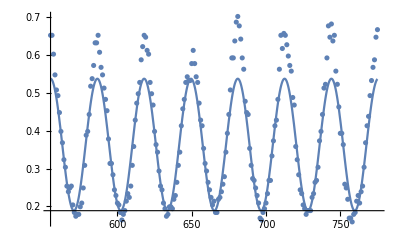

{a1→1,a2→0.8,μx1→555,w2→20,μx2→31.5}

```mathematica
n=7;
model= a1 (1-a2 Sum[ Exp[(-2(x-μx2*(j+0.5)-μx1)^2)/w2^2],{j,-n,n}]);
params = {a1->1,a2->0.8,μx1->xi,w2->20,μx2->31.5};
Show[Plot[model/.params,{x,xi,xf},PlotRange->All],ListPlot[linedata]]
params
```

```mathematica
fit=FindFit[data,model,{{a1,1},{a2,0.8},{μx1,xi},{μx2,31.5},{w2,20}},x]
```

{a1→8.574,a2→0.817461,μx1→555.665,μx2→31.3727,w2→29.2568}

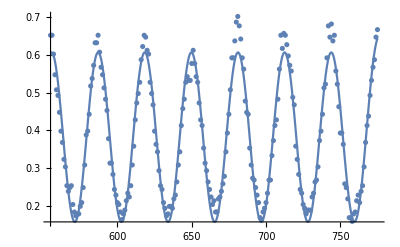

{a1→8.574,a2→0.817461,μx1→555.665,μx2→31.3727,w2→29.2568}

```mathematica
Show[Plot[model/.fit,{x,xi,xf},PlotRange->All],ListPlot[data]]
fit
```

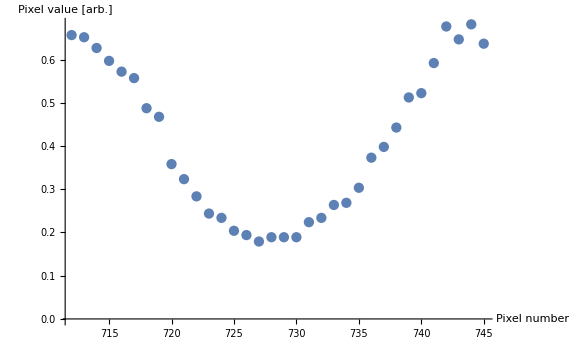

```mathematica
(*now do a fit to get a better Gaussian fit*)
dx=40;
xi=752-dx;
xf=785-dx;
linedata=Transpose@{Range[xi,xf],data[[rows-y2+i;;rows-y1+i, xi;;xf]][[1]]};
ListPlot[linedata,Joined->False,LabelStyle->Directive[Black, Medium],AxesLabel-> {"Pixel number","Pixel value [arb.]"},ImageSize->Large,PlotRange->All]
```

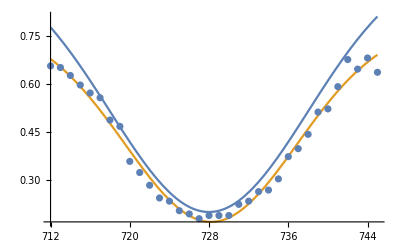

{a1→0.786529,a2→0.785099,μx1→728.205,w1→17.3612}

```mathematica
model= a1 (1-a2  Exp[(-2(x-μx1)^2)/w1^2]);
params = {a1->1,a2->0.8,μx1->xi+16,w1->20};
fit=FindFit[linedata,model,{{a1,1},{a2,0.8},{μx1,xi+16},{w1,20}},x];
Show[Plot[{model/.params,model/.fit},{x,xi,xf},PlotRange->All],ListPlot[linedata]]
fit
```

```mathematica
fit/.params,{x,xi,xf},PlotRange->All]
```

Can use the known period of the fabricated array mask to calibrate the image.

```mathematica
""
```

```mathematica
"Pixels per realspace um in mask plane"
α=31.3727/430
"Site waist w0 at atoms, um"
mag = (75/250)(30/200)(22.3/150); (*mask to atoms magnification*)
(17.3612/α)*mag
```

Pixels per realspace um in mask plane

0.0729598

Site waist w0 at atoms, um

1.59192

```mathematica
mag
```

0.00669

### 3D analysis

```mathematica
imagedir="trap_array_images\\20220119_focal_scan\\";
imagedir =FileNameJoin[{NotebookDirectory[],imagedir}];
SetDirectory[imagedir];
```

```mathematica
(*the distances in the filenames might be inaccurate. use the axial position data from my Field Notes*)
fnames = {
"20220119 trap image focal point.tif","20220119 trap image focal point +0.2mm.tif",
"20220119 trap image focal point +0.4mm.tif","20220119 trap image focal point +0.6mm.tif","20220119 trap image focal point +0.8mm.tif","20220119 trap image focal point +1.0mm.tif","20220119 trap image focal point +1.2mm.tif","20220119 trap image focal point +1.3mm.tif","20220119 trap image focal point +1.5mm.tif","20220119 trap image focal point +1.7mm.tif","20220119 trap image focal point +1.9mm.tif","20220119 trap image focal point +2.1mm.tif","20220119 trap image focal point +2.3mm.tif","20220119 trap image focal point +2.5mm.tif","20220119 trap image focal point +2.7mm.tif","20220119 trap image focal point +2.9mm.tif","20220119 trap image focal point +3.1mm.tif","20220119 trap image focal point +3.3mm.tif",
"20220119 trap image focal point +3.5mm.tif"
};
(*marked images for being able to tell which site is which when we are tracking it axially*)
(*fnames = Table[ToString[StringForm["trap_image_zstep_``.tif",i]],{i,Range[19]}];*)
site1coords = {{779,543},{775,543},{776,544},{776,543},{769,545},{777,524},{793,523},{795,528},{792,530},{790,529},{784,628},{792,530},{778,526},{776,525},{781,526},{775,529},{775,528},{774,530},{770,525}};
site2coords = {{842,639},{841,639},{842,640},{832,638},{842,640},{853,619},{858,620},{861,623},{857,624},{854,624},{849,624},{849,623},{844,624},{840,621},{843,620},{837,623},{838,624},{834,620},{834,620}};
```

```mathematica
img =Import[fnames[[1]]];
(*img = ColorConvert[Import[fnames[[1]]],"grayscale"];*)
phi=-0.045;
(*data = ImageData[ImageRotate[img,phi],Automatic];*)
data = ImageData[img,Automatic];
data =  data/Max[data];
rows = data//Length;
cols= data[[6]]//Length;
y1=rows/2;
y2 =y1+50;
Show[Image[data],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{1,y1},{cols,y2}]}],ImageSize->Medium]
```

-Graphics-

```mathematica
site = data[[rows-y2+8;;rows-y1-10, cols/2+20;;cols/2+53]];
Image[site]
```

-Graphics-

```mathematica
{x0,y0} = site1coords[[1]];
site = data[[y0-15;;y0+15, x0-15;;x0+15]];
Image[site]
```

-Graphics-

```mathematica
site//Dimensions
```

{31,31}

```mathematica
ListPlot[site[[18,;;,2]]]
```

Part::partd: Part specification {{312/341,31/33,317/341,312/341,305/341,920/1023,306/341,916/1023,914/1023,932/1023,926/1023,943/1023,316/341,928/1023,314/341,959/1023,317/341,937/1023,925/1023,304/341,901/1023,898/1023,27/31,877/1023,874/1023,862/1023,887/1023,303/341,908/1023,914/1023,296/341},«29»,{85/93,941/1023,31/33,958/1023,31/33,971/1023,315/341,326/341,967/1023,958/1023,980/1023,320/341,964/1023,327/341,88/93,32/33,320/341,988/1023,956/1023,325/341,947/1023,941/1023,86/93,928/1023,931/1023,10/11,306/341,311/341,919/1023,315/341,973/1023}}⟦18,1;;All,2⟧ is longer than depth of object.

Part::partd: Part specification «1» is longer than depth of object.

Part::partd: Part specification {{0.914956,0.939394,0.929619,0.914956,0.894428,0.899316,0.897361,0.895406,0.893451,0.911046,0.905181,0.921799,0.926686,0.907136,0.920821,0.937439,0.929619,0.915934,0.904203,0.891496,0.880743,0.87781,0.870968,0.857283,0.85435,0.84262,0.867058,0.888563,0.887586,0.893451,0.868035},«29»,{0.913978,«29»,0.951124}}⟦«1»⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListPlot::lpn: {{0.914956,0.939394,0.929619,0.914956,0.894428,0.899316,0.897361,0.895406,0.893451,0.911046,0.905181,0.921799,0.926686,0.907136,0.920821,0.937439,0.929619,0.915934,0.904203,0.891496,0.880743,0.87781,0.870968,0.857283,0.85435,0.84262,0.867058,0.888563,0.887586,0.893451,0.868035},«29»,{0.913978,«29»,0.951124}}⟦«1»⟧ is not a list of numbers or pairs of numbers.

ListPlot[{{312/341,31/33,317/341,312/341,305/341,920/1023,306/341,916/1023,914/1023,932/1023,926/1023,943/1023,316/341,928/1023,314/341,959/1023,317/341,937/1023,925/1023,304/341,901/1023,898/1023,27/31,877/1023,874/1023,862/1023,887/1023,303/341,908/1023,914/1023,296/341},{29/31,953/1023,944/1023,941/1023,83/93,940/1023,925/1023,311/341,925/1023,929/1023,925/1023,313/341,10/11,931/1023,932/1023,934/1023,920/1023,908/1023,889/1023,914/1023,883/1023,856/1023,863/1023,283/341,859/1023,280/341,848/1023,857/1023,282/341,293/341,287/341},{85/93,916/1023,941/1023,934/1023,964/1023,947/1023,926/1023,311/341,919/1023,306/341,920/1023,955/1023,83/93,932/1023,926/1023,929/1023,922/1023,872/1023,28/33,838/1023,832/1023,818/1023,802/1023,258/341,773/1023,263/341,796/1023,799/1023,812/1023,74/93,77/93},{295/341,898/1023,929/1023,926/1023,931/1023,317/341,922/1023,931/1023,304/341,317/341,312/341,929/1023,916/1023,908/1023,893/1023,290/341,862/1023,844/1023,274/341,776/1023,252/341,749/1023,67/93,712/1023,237/341,21/31,239/341,709/1023,742/1023,755/1023,25/33},{844/1023,80/93,919/1023,307/341,937/1023,311/341,31/33,316/341,943/1023,950/1023,85/93,925/1023,305/341,910/1023,289/341,827/1023,796/1023,254/341,758/1023,697/1023,695/1023,683/1023,208/341,206/341,614/1023,617/1023,208/341,632/1023,661/1023,676/1023,241/341},{809/1023,851/1023,874/1023,890/1023,10/11,932/1023,312/341,967/1023,31/33,929/1023,925/1023,905/1023,898/1023,863/1023,835/1023,794/1023,745/1023,701/1023,659/1023,56/93,200/341,189/341,542/1023,16/31,511/1023,171/341,544/1023,569/1023,565/1023,199/341,641/1023},{757/1023,784/1023,282/341,287/341,908/1023,10/11,316/341,929/1023,324/341,959/1023,920/1023,911/1023,853/1023,815/1023,767/1023,245/341,677/1023,213/341,581/1023,542/1023,500/1023,43/93,144/341,427/1023,38/93,431/1023,427/1023,446/1023,478/1023,530/1023,554/1023},{674/1023,251/341,785/1023,841/1023,288/341,303/341,943/1023,944/1023,962/1023,947/1023,931/1023,884/1023,281/341,799/1023,725/1023,228/341,623/1023,188/341,505/1023,153/341,141/341,380/1023,362/1023,116/341,112/341,113/341,349/1023,362/1023,388/1023,436/1023,490/1023},{211/341,229/341,746/1023,265/341,863/1023,889/1023,83/93,916/1023,932/1023,934/1023,905/1023,850/1023,808/1023,23/31,21/31,206/341,544/1023,485/1023,40/93,131/341,113/341,298/1023,289/1023,272/1023,256/1023,84/341,3/11,284/1023,107/341,361/1023,428/1023},{548/1023,644/1023,691/1023,764/1023,272/341,289/341,896/1023,29/33,925/1023,82/93,878/1023,835/1023,784/1023,23/33,58/93,565/1023,497/1023,140/341,126/341,322/1023,277/1023,250/1023,7/33,206/1023,64/341,63/341,206/1023,229/1023,250/1023,296/1023,344/1023},{164/341,17/31,647/1023,710/1023,799/1023,283/341,299/341,914/1023,905/1023,893/1023,860/1023,800/1023,249/341,20/31,592/1023,169/341,146/341,376/1023,313/1023,272/1023,76/341,197/1023,182/1023,52/341,5/33,152/1023,152/1023,59/341,69/341,250/1023,295/1023},{431/1023,47/93,580/1023,691/1023,745/1023,273/341,77/93,27/31,889/1023,866/1023,856/1023,256/341,722/1023,216/341,568/1023,475/1023,12/31,113/341,283/1023,229/1023,197/1023,163/1023,49/341,43/341,119/1023,4/33,41/341,4/31,52/341,202/1023,83/341},{127/341,157/341,548/1023,59/93,736/1023,776/1023,9/11,862/1023,877/1023,862/1023,278/341,758/1023,689/1023,629/1023,524/1023,430/1023,123/341,314/1023,257/1023,19/93,56/341,5/33,45/341,113/1023,34/341,107/1023,34/341,38/341,4/31,160/1023,72/341},{353/1023,142/341,511/1023,203/341,703/1023,250/341,830/1023,285/341,875/1023,841/1023,269/341,746/1023,225/341,196/341,171/341,139/341,32/93,96/341,83/341,64/341,56/341,5/33,125/1023,115/1023,34/341,89/1023,8/93,101/1023,118/1023,158/1023,65/341},{316/1023,13/33,44/93,53/93,664/1023,751/1023,791/1023,9/11,282/341,283/341,262/341,730/1023,224/341,569/1023,497/1023,140/341,113/341,97/341,236/1023,193/1023,164/1023,145/1023,41/341,119/1023,36/341,91/1023,1/11,92/1023,10/93,4/31,185/1023},{96/341,11/31,464/1023,563/1023,59/93,240/341,785/1023,823/1023,851/1023,821/1023,797/1023,245/341,659/1023,53/93,485/1023,134/341,32/93,289/1023,232/1023,194/1023,163/1023,145/1023,134/1023,113/1023,34/341,95/1023,30/341,3/31,37/341,43/341,184/1023},{95/341,34/93,150/341,185/341,635/1023,237/341,24/31,817/1023,278/341,815/1023,815/1023,67/93,670/1023,592/1023,502/1023,427/1023,353/1023,301/1023,241/1023,196/1023,16/93,14/93,136/1023,4/33,37/341,34/341,97/1023,3/31,119/1023,148/1023,193/1023},{287/1023,350/1023,151/341,182/341,213/341,719/1023,782/1023,277/341,850/1023,839/1023,24/31,751/1023,692/1023,196/341,178/341,445/1023,373/1023,29/93,256/1023,223/1023,16/93,167/1023,50/341,42/341,38/341,37/341,37/341,115/1023,42/341,166/1023,206/1023},{101/341,125/341,158/341,562/1023,222/341,238/341,25/33,811/1023,282/341,848/1023,821/1023,23/31,692/1023,628/1023,541/1023,470/1023,395/1023,325/1023,280/1023,80/341,67/341,16/93,158/1023,48/341,130/1023,41/341,40/341,140/1023,149/1023,61/341,230/1023},{10/31,134/341,164/341,593/1023,2/3,725/1023,268/341,833/1023,860/1023,851/1023,818/1023,782/1023,237/341,215/341,193/341,167/341,142/341,371/1023,307/1023,87/341,235/1023,208/1023,182/1023,53/341,145/1023,13/93,151/1023,52/341,60/341,73/341,278/1023},{350/1023,442/1023,175/341,598/1023,701/1023,773/1023,833/1023,283/341,877/1023,293/341,850/1023,800/1023,746/1023,61/93,608/1023,554/1023,482/1023,413/1023,11/31,298/1023,266/1023,82/341,205/1023,65/341,59/341,172/1023,60/341,202/1023,78/341,269/1023,325/1023},{13/33,469/1023,569/1023,7/11,722/1023,799/1023,283/341,884/1023,298/341,895/1023,895/1023,832/1023,791/1023,234/341,223/341,599/1023,526/1023,469/1023,410/1023,361/1023,104/341,277/1023,256/1023,80/341,235/1023,230/1023,79/341,250/1023,96/341,335/1023,127/341},{151/341,541/1023,610/1023,694/1023,761/1023,817/1023,859/1023,29/33,925/1023,908/1023,299/341,853/1023,25/31,772/1023,234/341,216/341,580/1023,177/341,159/341,144/341,382/1023,347/1023,316/1023,302/1023,290/1023,287/1023,317/1023,10/31,362/1023,400/1023,452/1023},{520/1023,602/1023,673/1023,247/341,24/31,859/1023,298/341,911/1023,947/1023,316/341,298/341,887/1023,284/341,269/341,766/1023,21/31,659/1023,596/1023,538/1023,494/1023,153/341,13/31,13/33,394/1023,125/341,376/1023,397/1023,137/341,449/1023,163/341,181/341},{580/1023,219/341,700/1023,791/1023,26/33,289/341,305/341,311/341,958/1023,955/1023,947/1023,908/1023,895/1023,851/1023,73/93,23/31,725/1023,223/341,626/1023,587/1023,548/1023,508/1023,479/1023,481/1023,158/341,475/1023,162/341,521/1023,181/341,580/1023,635/1023},{664/1023,722/1023,758/1023,271/341,26/31,304/341,85/93,86/93,88/93,962/1023,925/1023,314/341,919/1023,877/1023,853/1023,9/11,787/1023,740/1023,712/1023,226/341,644/1023,210/341,53/93,574/1023,192/341,586/1023,602/1023,204/341,58/93,673/1023,718/1023},{724/1023,773/1023,812/1023,860/1023,878/1023,28/31,953/1023,959/1023,964/1023,317/341,327/341,323/341,958/1023,931/1023,82/93,883/1023,860/1023,811/1023,259/341,749/1023,719/1023,23/33,229/341,224/341,676/1023,224/341,2/3,706/1023,739/1023,68/93,776/1023},{262/341,25/31,845/1023,83/93,85/93,315/341,953/1023,29/31,323/341,321/341,985/1023,974/1023,967/1023,949/1023,311/341,907/1023,881/1023,290/341,281/341,823/1023,270/341,782/1023,71/93,779/1023,255/341,760/1023,258/341,785/1023,805/1023,827/1023,826/1023},{28/33,290/341,27/31,922/1023,309/341,317/341,956/1023,962/1023,970/1023,89/93,955/1023,953/1023,970/1023,962/1023,322/341,941/1023,10/11,943/1023,301/341,887/1023,287/341,874/1023,272/341,854/1023,844/1023,860/1023,853/1023,77/93,872/1023,82/93,303/341},{904/1023,314/341,941/1023,940/1023,312/341,29/31,980/1023,967/1023,320/341,956/1023,973/1023,318/341,329/341,89/93,977/1023,318/341,316/341,958/1023,937/1023,941/1023,85/93,85/93,301/341,294/341,893/1023,295/341,884/1023,301/341,83/93,309/341,944/1023},{85/93,941/1023,31/33,958/1023,31/33,971/1023,315/341,326/341,967/1023,958/1023,980/1023,320/341,964/1023,327/341,88/93,32/33,320/341,988/1023,956/1023,325/341,947/1023,941/1023,86/93,928/1023,931/1023,10/11,306/341,311/341,919/1023,315/341,973/1023}}⟦18,1;;All,2⟧]

```mathematica
profiles = {};
model = A (1-   Exp[(-((x-μx)^2+(y-μy)^2))/σ^2]);
i=1;
img =Import[fnames[[i]]];
phi=-0.045;data = ImageData[ImageRotate[img,phi],Automatic];
data =  data/Max[data];
cols = 
img = Image[data];
{x0,y0} = site1coords[[i]];
site = data[[y0-15;;y0+15, x0-15;;x0+15]];
(*Export[ToString[StringForm["trap_image_zstep_``.tif",i]],img];*)
(*AppendTo[profiles,site[[18,;;]]];*)
```

```mathematica
Image[site]
```

-Graphics-

```mathematica
site//Dimensions
```

{31,31}

```mathematica
(*ATTENTION: "fnames" must be the list of unmarked images at this step! go back and rerun that cell with the table of fnames commented out*)
```

```mathematica
xyf = {};(*Table of {row,col,f} entries where f is the image val at row,col*)
rows = site//Length;
cols= site[[1]]//Length;
For[i=1,i<rows+1,i++,
xyf=Join[xyf,Table[{i,j,site[[i,j]]},{j,Range[cols]}]]
]
```

```mathematica
xyf//Dimensions
```

{961,3}

```mathematica
Clear[μx,μy]
fit =FindFit[xyf,model,{{μy,15},{μx,15},σ,A},{y,x}]
yy=fit[[1]][[2]]
xx=fit[[2]][[2]]
```

{μy→19.065,μx→17.1577,σ→11.704,A→1.01727}

19.065

17.1577

```mathematica
fit
```

{μx→19.065,μy→17.1577,σ→11.704,A→1.01727}

19.065

17.1577

```mathematica
19.065011066969216
```

19.065

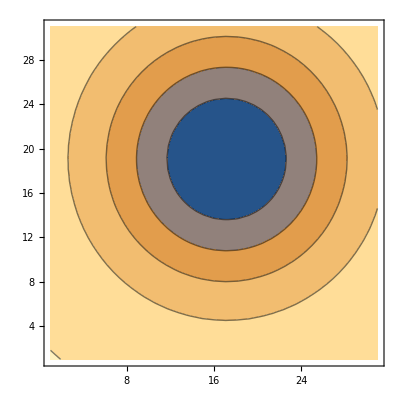

```mathematica
ContourPlot[model/.fit,{x,1,rows},{y,1,cols}]
```

```mathematica
Floor[yy+0.5]
```

17

```mathematica
x0
```

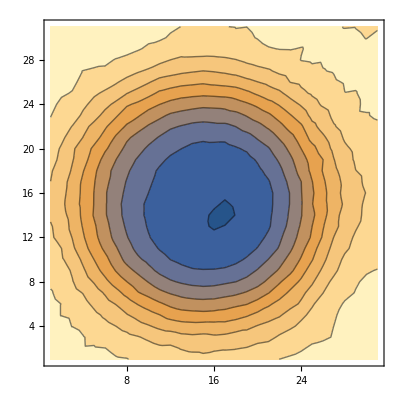

```mathematica
ox=x0-15;
oy=y0-15;
site = data[[oy+Floor[yy+0.5]-15;;oy+Floor[yy+0.5]+15, ox+Floor[xx+0.5]-15;;ox+Floor[xx+0.5]+15]];
ListContourPlot[site]
```

```mathematica
k=5;
img =Import[fnames[[k]]];
phi=-0.045;data = ImageData[ImageRotate[img,phi],Automatic];
data =  data/Max[data];
cols = 
img = Image[data];
{x0,y0} = site1coords[[k]];
site = data[[y0-15;;y0+15, x0-15;;x0+15]];
xyf = {};(*Table of {row,col,f} entries where f is the image val at row,col*)
rows = site//Length;
cols= site[[1]]//Length;
For[i=1,i<rows+1,i++,
xyf=Join[xyf,Table[{i,j,site[[i,j]]},{j,Range[cols]}]]
];
fit =FindFit[xyf,model,{{μy,15},{μx,15},σ,A},{y,x}];
yy=fit[[1]][[2]];
xx=fit[[2]][[2]];
ox=x0-15;
oy=y0-15;
adjustedsite = data[[oy+Floor[yy+0.5]-15;;oy+Floor[yy+0.5]+15, ox+Floor[xx+0.5]-15;;ox+Floor[xx+0.5]+15]];
AppendTo[sites,site];
Print[Image[site],Image[adjustedsite]]
```

AppendTo::rvalue: sites is not a variable with a value, so its value cannot be changed.

-Graphics--Graphics-

```mathematica
sites = {};
slicesx={};
slicesy={};
For[k=1,k<Length[fnames]+1,k++,
img =Import[fnames[[k]]];
phi=-0.045;data = ImageData[ImageRotate[img,phi],Automatic];
If[k==1,norm=Max[data],norm];
data =  data/norm;
cols = 
img = Image[data];
{x0,y0} = site1coords[[k]];
site = data[[y0-15;;y0+15, x0-15;;x0+15]];
xyf = {};(*Table of {row,col,f} entries where f is the image val at row,col*)
rows = site//Length;
cols= site[[1]]//Length;
For[i=1,i<rows+1,i++,
xyf=Join[xyf,Table[{i,j,site[[i,j]]},{j,Range[cols]}]]
];
fit =FindFit[xyf,model,{{μy,15},{μx,15},σ,A},{y,x}];
yy=fit[[1]][[2]];
xx=fit[[2]][[2]];
ox=x0-15;
oy=y0-15;
adjustedsite = data[[oy+Floor[yy+0.5]-15;;oy+Floor[yy+0.5]+15, ox+Floor[xx+0.5]-15;;ox+Floor[xx+0.5]+15]];
AppendTo[slicesx,adjustedsite[[15,;;]]];
AppendTo[slicesy,adjustedsite[[15,;;]]];
AppendTo[sites,adjustedsite];
Print[Image[site],Image[adjustedsite]];
Export[ToString[StringForm["site_zstep``.csv",k]], adjustedsite];
](*images on the left are not position corrected, while the rightside ones have been fit and centered*)
```

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

«16 more identical outputs»

```mathematica
Image[sites[[1]],ImageSize->Medium]
```

-Graphics-

C:\Users\prest\Documents\Graduate Research\amo-mathematica\lab_analysis\

```mathematica
Export[FileNameJoin[{NotebookDirectory[],ToString[StringForm["site_zstep``.csv",1]]}], sites[[1]]//N]
```

C:\Users\prest\Documents\Graduate Research\amo-mathematica\lab_analysis\site_zstep1.csv

```mathematica
ListPlot3D[slicesy]
ListPlot3D[slicesx]
```

-Graphics3D-

-Graphics3D-

```mathematica
Export["test.csv",slicesx//N]
```

test.csv

```mathematica
ToString[StringForm["site_zstep``.csv",k]]
```

site_zstep20.csv

```mathematica
NotebookDirectory[]
```

C:\Users\prest\Documents\Graduate Research\amo-mathematica\lab_analysis\

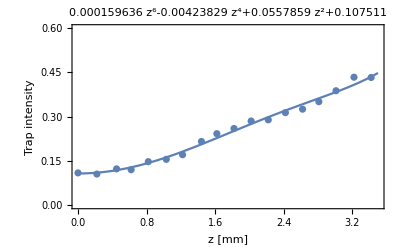

```mathematica
zmodel =A+a z^2+b z^4+c z^6(*+d z^8+f z^10+g z^12*);
axial=Table[sites[[i]][[15,15]],{i,Range[Length[fnames]]}];
zpts = {.08,0.3,0.53,0.7,0.9,1.11,1.3,1.52,1.7,1.9,2.1,2.3,2.5,2.7,2.89,3.09,3.3,3.5,3.72}-0.08;
data =Transpose@{zpts,axial};
fit = FindFit[data,zmodel,{A,a,b,c(*,d,f,g*)},z];
Show[Plot[zmodel/.fit,{z,0,3.5},PlotRange->{0,0.6}],
ListPlot[data],PlotLabel->zmodel/.fit,Frame->True,Axes->False,FrameLabel->{"z [mm]","Trap intensity"},LabelStyle->Directive[FontSize->12,Black]]
```

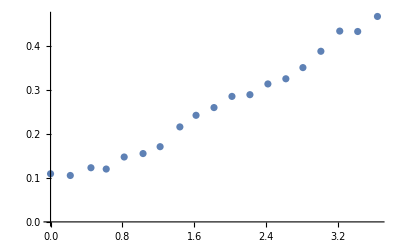

```mathematica
ListPlot[data]
```

```mathematica
,
```

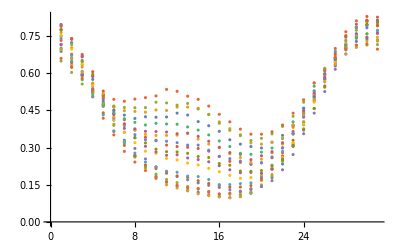

```mathematica
ListPlot[Table[sites[[i]][[15]],{i,Range[Length[fnames]]}]]
```

```mathematica
sites[[1]]//Dimensions
```

{31,31}

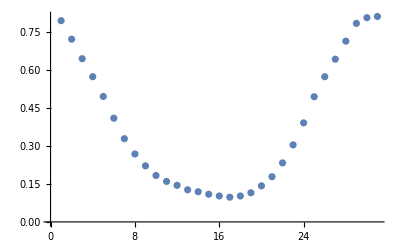

```mathematica
ListPlot[sites[[1]][[15,;;]]]
```

```mathematica
i=4;
img =Import[fnames[[i]]];
data = ImageData[img,Automatic];
data =  data/Max[data];
img = Image[data];
{x0,y0} = site1coords[[i]];
site = data[[y0-15;;y0+15, x0-15;;x0+15]];
Image[site]
```

-Graphics-

```mathematica
profiles = {};
For[i=1,i<Length[fnames]+1,i++,
img =Import[fnames[[i]]];
(*phi=-0.045;data = ImageData[ImageRotate[img,phi],Automatic];*)
data = ImageData[img,Automatic];
data =  data/Max[data];
img = Image[data];
{x0,y0} = site1coords[[i]];
site = data[[y0-15;;y0+15, x0-15;;x0+15]];
(*Export[ToString[StringForm["trap_image_zstep_``.tif",i]],img];*)
(*rows = data//Length;
cols= data[[1]]//Length;
y1=rows/2;
y2 =y1+50;
site =data[[rows-y2+5;;rows-y1-10, cols/2-15;;cols/2+17 ]];*)
(*AppendTo[profiles,site[[18,;;]]];*)
Print[Image[site]]
]
```

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

Part::partw: Part 19 of {{779,543},{775,543},{776,544},{779,543},{783,524},{789,524},{793,523},{795,528},{792,530},{790,529},{784,628},{784,527},{778,526},{776,525},{781,526},{775,529},{775,528},{770,525}} does not exist.

Set::shape: Lists {x0,y0} and {{779,543},{775,543},{776,544},{779,543},{783,524},{789,524},{793,523},{795,528},{792,530},{790,529},{784,628},{784,527},{778,526},{776,525},{781,526},{775,529},{775,528},{770,525}}⟦19⟧ are not the same shape.

-Graphics-

$Aborted

```mathematica
Image[site]
```

-Graphics-

```mathematica
NotebookDirectory[]
```

C:\Users\prest\Documents\Graduate Research\amo-mathematica\lab_analysis\

```mathematica
imagedir
```

C:\Users\prest\Documents\Graduate Research\amo-mathematica\lab_analysis\trap_array_images\20220119_focal_scan

```mathematica
ToString[Evaluate[FileNameJoin[{imagedir,StringForm["trap_image_zstep_``.tif",i]}]]]
```

FileNameJoin[{trap_array_images\20220119_focal_scan, trap_image_zstep_20.tif}]

```mathematica
FileNameJoin[{imagedir,ToString[StringForm["trap_image_zstep_``.tif",i]]}]
```

trap_array_images\20220119_focal_scan\trap_image_zstep_20.tif

```mathematica
..
```

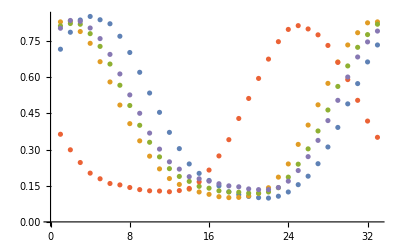

```mathematica
ListPlot[profiles[[;;5]]]
```

```mathematica
ListPlot3D[profiles]
```

-Graphics3D-

### 2D analysis

```mathematica
fnames = {"2021-12-29-100748 trap image (iris opened).png", "2021-12-29-100748 trap image (iris closed).png"};
```

```mathematica
img =  ColorConvert[Import[fnames[[1]]],"grayscale"];
phi=-0.045;
Show[ImageRotate[img,phi], ImageSize-> Medium]
```

-Graphics-

```mathematica
data = ImageData[ImageRotate[img,phi]];
data = data-data[[50,50]];(*subtract off the background*)
data = Replace[data,_?Negative-> 0,{2}]; 
data = data/Max[data]; 
rows = data//Length;
cols= data[[1]]//Length;
```

```mathematica
(*x1=485;
x2=495;*)
y1=lenx/2
y2 =y1+10
Show[Image[data],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{1,y1},{cols,y2}]}],ImageSize->Medium]
```

322

332

-Graphics-

```mathematica
data//Dimensions
```

```mathematica
{644,835}
```

```mathematica
leny/2
```

835/2

```mathematica
Image[data[[rows-y2+5;;rows-y1-3, 1;; leny]]]
```

-Graphics-

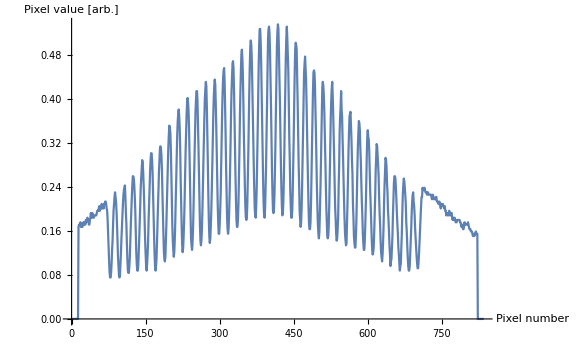

```mathematica
i=-1;
linedata = Transpose@{Range[leny],data[[rows-y2+4;;rows-y1-4, 1;; leny]][[1]]};
ListPlot[linedata, Joined->True,AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Large]
```

```mathematica
ListPlot[linedata[[960;;1100]],Joined->True,LabelStyle->Directive[Black, Medium],AxesLabel-> {"Pixel number","Pixel value [arb.]"},ImageSize->Large]
```

Part::take: Cannot take positions 960 through 1100 in {{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.},{8,0.},{9,0.},{10,0.},{11,0.},{12,0.},{13,0.},{14,0.167364},{15,0.171548},{16,0.171548},{17,0.171548},«18»,{36,0.171548},{37,0.179916},{38,0.1841},{39,0.192469},{40,0.188285},{41,0.1841},{42,0.192469},{43,0.188285},{44,0.1841},{45,0.1841},{46,0.188285},{47,0.188285},{48,0.188285},{49,0.188285},{50,0.188285},«785»}.

Part::take: Cannot take positions 960 through 1100 in {{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},{11.,0.},{12.,0.},{13.,0.},{14.,0.167364},«24»,{39.,0.192469},{40.,0.188285},{41.,0.1841},{42.,0.192469},{43.,0.188285},{44.,0.1841},{45.,0.1841},{46.,0.188285},{47.,0.188285},{48.,0.188285},{49.,0.188285},{50.,0.188285},«785»}.

Part::take: Cannot take positions 960 through 1100 in {{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},{11.,0.},{12.,0.},{13.,0.},{14.,0.167364},{15.,0.171548},«21»,{37.,0.179916},{38.,0.1841},{39.,0.192469},{40.,0.188285},{41.,0.1841},{42.,0.192469},{43.,0.188285},{44.,0.1841},{45.,0.1841},{46.,0.188285},{47.,0.188285},{48.,0.188285},{49.,0.188285},{50.,0.188285},«785»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

ListPlot::lpn: {{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},{11.,0.},{12.,0.},{13.,0.},{14.,0.167364},{15.,0.171548},«21»,{37.,0.179916},{38.,0.1841},{39.,0.192469},{40.,0.188285},{41.,0.1841},{42.,0.192469},{43.,0.188285},{44.,0.1841},{45.,0.1841},{46.,0.188285},{47.,0.188285},{48.,0.188285},{49.,0.188285},{50.,0.188285},«785»}⟦960;;1100⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.},{8,0.},{9,0.},{10,0.},{11,0.},{12,0.},{13,0.},{14,0.167364},{15,0.171548},{16,0.171548},{17,0.171548},{18,0.175732},{19,0.167364},{20,0.171548},{21,0.167364},{22,0.167364},{23,0.171548},{24,0.175732},{25,0.171548},{26,0.175732},{27,0.171548},{28,0.171548},{29,0.179916},{30,0.175732},{31,0.179916},{32,0.1841},{33,0.179916},{34,0.179916},{35,0.171548},{36,0.171548},{37,0.179916},{38,0.1841},{39,0.192469},{40,0.188285},{41,0.1841},{42,0.192469},{43,0.188285},{44,0.1841},{45,0.1841},{46,0.188285},{47,0.188285},{48,0.188285},{49,0.188285},{50,0.188285},{51,0.192469},{52,0.196653},{53,0.196653},{54,0.196653},{55,0.200837},{56,0.205021},{57,0.196653},{58,0.200837},{59,0.200837},{60,0.200837},{61,0.209205},{62,0.200837},{63,0.205021},{64,0.205021},{65,0.200837},{66,0.209205},{67,0.209205},{68,0.213389},{69,0.213389},{70,0.209205},{71,0.200837},{72,0.196653},{73,0.179916},{74,0.154812},{75,0.129707},{76,0.104603},{77,0.083682},{78,0.0753138},{79,0.0753138},{80,0.083682},{81,0.100418},{82,0.125523},{83,0.142259},{84,0.171548},{85,0.196653},{86,0.209205},{87,0.221757},{88,0.230126},{89,0.221757},{90,0.213389},{91,0.196653},{92,0.171548},{93,0.142259},{94,0.112971},{95,0.0962343},{96,0.0794979},{97,0.0753138},{98,0.0794979},{99,0.100418},{100,0.121339},{101,0.146444},{102,0.167364},{103,0.188285},{104,0.209205},{105,0.225941},{106,0.23431},{107,0.238494},{108,0.242678},{109,0.221757},{110,0.192469},{111,0.171548},{112,0.138075},{113,0.108787},{114,0.0878661},{115,0.083682},{116,0.083682},{117,0.0962343},{118,0.112971},{119,0.142259},{120,0.171548},{121,0.196653},{122,0.221757},{123,0.242678},{124,0.259414},{125,0.259414},{126,0.25523},{127,0.242678},{128,0.221757},{129,0.196653},{130,0.158996},{131,0.121339},{132,0.100418},{133,0.0878661},{134,0.0878661},{135,0.0962343},{136,0.121339},{137,0.146444},{138,0.175732},{139,0.205021},{140,0.238494},{141,0.25523},{142,0.271967},{143,0.288703},{144,0.284519},{145,0.267782},{146,0.242678},{147,0.213389},{148,0.175732},{149,0.142259},{150,0.117155},{151,0.0962343},{152,0.0878661},{153,0.100418},{154,0.117155},{155,0.142259},{156,0.179916},{157,0.209205},{158,0.238494},{159,0.267782},{160,0.288703},{161,0.301255},{162,0.301255},{163,0.288703},{164,0.267782},{165,0.230126},{166,0.192469},{167,0.154812},{168,0.121339},{169,0.0962343},{170,0.0878661},{171,0.0962343},{172,0.108787},{173,0.138075},{174,0.171548},{175,0.205021},{176,0.23431},{177,0.267782},{178,0.288703},{179,0.309623},{180,0.313808},{181,0.309623},{182,0.297071},{183,0.271967},{184,0.230126},{185,0.192469},{186,0.154812},{187,0.121339},{188,0.108787},{189,0.104603},{190,0.112971},{191,0.142259},{192,0.171548},{193,0.209205},{194,0.242678},{195,0.280335},{196,0.313808},{197,0.334728},{198,0.351464},{199,0.34728},{200,0.338912},{201,0.309623},{202,0.267782},{203,0.221757},{204,0.171548},{205,0.142259},{206,0.125523},{207,0.112971},{208,0.121339},{209,0.142259},{210,0.175732},{211,0.217573},{212,0.25523},{213,0.297071},{214,0.334728},{215,0.359833},{216,0.372385},{217,0.380753},{218,0.368201},{219,0.34728},{220,0.309623},{221,0.251046},{222,0.209205},{223,0.167364},{224,0.133891},{225,0.121339},{226,0.129707},{227,0.150628},{228,0.179916},{229,0.217573},{230,0.263598},{231,0.305439},{232,0.338912},{233,0.372385},{234,0.393305},{235,0.401674},{236,0.393305},{237,0.376569},{238,0.343096},{239,0.292887},{240,0.242678},{241,0.188285},{242,0.146444},{243,0.133891},{244,0.125523},{245,0.138075},{246,0.16318},{247,0.200837},{248,0.251046},{249,0.292887},{250,0.334728},{251,0.376569},{252,0.39749},{253,0.414226},{254,0.414226},{255,0.39749},{256,0.355649},{257,0.313808},{258,0.267782},{259,0.217573},{260,0.171548},{261,0.142259},{262,0.133891},{263,0.142259},{264,0.16318},{265,0.196653},{266,0.238494},{267,0.284519},{268,0.32636},{269,0.368201},{270,0.401674},{271,0.41841},{272,0.430962},{273,0.422594},{274,0.384937},{275,0.334728},{276,0.284519},{277,0.225941},{278,0.179916},{279,0.150628},{280,0.138075},{281,0.146444},{282,0.167364},{283,0.196653},{284,0.23431},{285,0.276151},{286,0.322176},{287,0.368201},{288,0.401674},{289,0.422594},{290,0.435146},{291,0.426778},{292,0.393305},{293,0.351464},{294,0.305439},{295,0.25523},{296,0.209205},{297,0.175732},{298,0.154812},{299,0.154812},{300,0.171548},{301,0.196653},{302,0.225941},{303,0.276151},{304,0.32636},{305,0.376569},{306,0.414226},{307,0.439331},{308,0.451883},{309,0.456067},{310,0.430962},{311,0.384937},{312,0.334728},{313,0.276151},{314,0.230126},{315,0.1841},{316,0.16318},{317,0.154812},{318,0.16318},{319,0.188285},{320,0.221757},{321,0.267782},{322,0.317992},{323,0.372385},{324,0.414226},{325,0.439331},{326,0.464435},{327,0.468619},{328,0.456067},{329,0.41841},{330,0.368201},{331,0.313808},{332,0.259414},{333,0.217573},{334,0.179916},{335,0.167364},{336,0.167364},{337,0.179916},{338,0.209205},{339,0.25523},{340,0.305439},{341,0.368201},{342,0.414226},{343,0.451883},{344,0.481172},{345,0.48954},{346,0.472803},{347,0.443515},{348,0.393305},{349,0.334728},{350,0.288703},{351,0.242678},{352,0.205021},{353,0.1841},{354,0.179916},{355,0.1841},{356,0.209205},{357,0.25523},{358,0.301255},{359,0.359833},{360,0.414226},{361,0.460251},{362,0.493724},{363,0.506276},{364,0.497908},{365,0.472803},{366,0.430962},{367,0.380753},{368,0.330544},{369,0.280335},{370,0.238494},{371,0.200837},{372,0.188285},{373,0.1841},{374,0.205021},{375,0.238494},{376,0.288703},{377,0.343096},{378,0.401674},{379,0.460251},{380,0.497908},{381,0.527197},{382,0.527197},{383,0.506276},{384,0.468619},{385,0.414226},{386,0.359833},{387,0.305439},{388,0.251046},{389,0.209205},{390,0.188285},{391,0.1841},{392,0.200837},{393,0.238494},{394,0.280335},{395,0.338912},{396,0.393305},{397,0.456067},{398,0.51046},{399,0.527197},{400,0.531381},{401,0.518828},{402,0.485356},{403,0.435146},{404,0.384937},{405,0.32636},{406,0.267782},{407,0.225941},{408,0.196653},{409,0.192469},{410,0.200837},{411,0.225941},{412,0.271967},{413,0.322176},{414,0.384937},{415,0.439331},{416,0.497908},{417,0.523013},{418,0.535565},{419,0.527197},{420,0.48954},{421,0.439331},{422,0.39749},{423,0.338912},{424,0.284519},{425,0.238494},{426,0.205021},{427,0.188285},{428,0.192469},{429,0.213389},{430,0.25523},{431,0.305439},{432,0.368201},{433,0.422594},{434,0.476987},{435,0.51046},{436,0.531381},{437,0.51046},{438,0.481172},{439,0.451883},{440,0.393305},{441,0.330544},{442,0.288703},{443,0.23431},{444,0.205021},{445,0.1841},{446,0.1841},{447,0.196653},{448,0.230126},{449,0.280335},{450,0.330544},{451,0.393305},{452,0.447699},{453,0.48954},{454,0.502092},{455,0.497908},{456,0.48954},{457,0.439331},{458,0.393305},{459,0.334728},{460,0.280335},{461,0.242678},{462,0.196653},{463,0.179916},{464,0.167364},{465,0.175732},{466,0.200837},{467,0.242678},{468,0.292887},{469,0.343096},{470,0.39749},{471,0.447699},{472,0.464435},{473,0.476987},{474,0.456067},{475,0.435146},{476,0.393305},{477,0.343096},{478,0.292887},{479,0.246862},{480,0.205021},{481,0.171548},{482,0.16318},{483,0.16318},{484,0.175732},{485,0.209205},{486,0.259414},{487,0.313808},{488,0.364017},{489,0.414226},{490,0.447699},{491,0.451883},{492,0.447699},{493,0.426778},{494,0.380753},{495,0.338912},{496,0.288703},{497,0.238494},{498,0.200837},{499,0.171548},{500,0.154812},{501,0.146444},{502,0.158996},{503,0.192469},{504,0.230126},{505,0.276151},{506,0.32636},{507,0.376569},{508,0.422594},{509,0.430962},{510,0.422594},{511,0.405858},{512,0.376569},{513,0.334728},{514,0.292887},{515,0.246862},{516,0.205021},{517,0.175732},{518,0.150628},{519,0.146444},{520,0.150628},{521,0.171548},{522,0.209205},{523,0.259414},{524,0.309623},{525,0.364017},{526,0.39749},{527,0.41841},{528,0.430962},{529,0.405858},{530,0.372385},{531,0.330544},{532,0.288703},{533,0.242678},{534,0.200837},{535,0.179916},{536,0.154812},{537,0.142259},{538,0.146444},{539,0.16318},{540,0.1841},{541,0.238494},{542,0.276151},{543,0.338912},{544,0.368201},{545,0.384937},{546,0.414226},{547,0.380753},{548,0.368201},{549,0.32636},{550,0.292887},{551,0.251046},{552,0.213389},{553,0.179916},{554,0.154812},{555,0.142259},{556,0.133891},{557,0.138075},{558,0.175732},{559,0.213389},{560,0.259414},{561,0.305439},{562,0.338912},{563,0.368201},{564,0.372385},{565,0.376569},{566,0.351464},{567,0.32636},{568,0.288703},{569,0.263598},{570,0.209205},{571,0.1841},{572,0.150628},{573,0.138075},{574,0.129707},{575,0.129707},{576,0.150628},{577,0.179916},{578,0.225941},{579,0.276151},{580,0.313808},{581,0.338912},{582,0.359833},{583,0.355649},{584,0.343096},{585,0.309623},{586,0.284519},{587,0.246862},{588,0.213389},{589,0.188285},{590,0.154812},{591,0.138075},{592,0.125523},{593,0.125523},{594,0.142259},{595,0.171548},{596,0.205021},{597,0.246862},{598,0.297071},{599,0.330544},{600,0.343096},{601,0.330544},{602,0.32636},{603,0.305439},{604,0.267782},{605,0.230126},{606,0.205021},{607,0.175732},{608,0.146444},{609,0.125523},{610,0.117155},{611,0.121339},{612,0.129707},{613,0.154812},{614,0.188285},{615,0.221757},{616,0.267782},{617,0.292887},{618,0.317992},{619,0.313808},{620,0.297071},{621,0.280335},{622,0.259414},{623,0.221757},{624,0.192469},{625,0.171548},{626,0.142259},{627,0.121339},{628,0.112971},{629,0.104603},{630,0.117155},{631,0.138075},{632,0.167364},{633,0.209205},{634,0.242678},{635,0.267782},{636,0.292887},{637,0.288703},{638,0.276151},{639,0.246862},{640,0.230126},{641,0.196653},{642,0.179916},{643,0.158996},{644,0.133891},{645,0.117155},{646,0.0962343},{647,0.104603},{648,0.108787},{649,0.129707},{650,0.150628},{651,0.188285},{652,0.217573},{653,0.246862},{654,0.259414},{655,0.259414},{656,0.25523},{657,0.238494},{658,0.217573},{659,0.192469},{660,0.171548},{661,0.154812},{662,0.129707},{663,0.117155},{664,0.100418},{665,0.0878661},{666,0.0962343},{667,0.100418},{668,0.129707},{669,0.154812},{670,0.192469},{671,0.225941},{672,0.242678},{673,0.25523},{674,0.251046},{675,0.238494},{676,0.225941},{677,0.209205},{678,0.175732},{679,0.158996},{680,0.133891},{681,0.112971},{682,0.0962343},{683,0.0878661},{684,0.0878661},{685,0.0962343},{686,0.117155},{687,0.142259},{688,0.16318},{689,0.192469},{690,0.213389},{691,0.225941},{692,0.230126},{693,0.213389},{694,0.205021},{695,0.188285},{696,0.16318},{697,0.146444},{698,0.129707},{699,0.112971},{700,0.100418},{701,0.0920502},{702,0.0920502},{703,0.104603},{704,0.121339},{705,0.142259},{706,0.16318},{707,0.1841},{708,0.205021},{709,0.221757},{710,0.221757},{711,0.238494},{712,0.23431},{713,0.23431},{714,0.23431},{715,0.238494},{716,0.23431},{717,0.230126},{718,0.230126},{719,0.230126},{720,0.225941},{721,0.230126},{722,0.230126},{723,0.225941},{724,0.225941},{725,0.225941},{726,0.225941},{727,0.225941},{728,0.225941},{729,0.221757},{730,0.217573},{731,0.221757},{732,0.225941},{733,0.221757},{734,0.217573},{735,0.217573},{736,0.217573},{737,0.217573},{738,0.221757},{739,0.221757},{740,0.213389},{741,0.213389},{742,0.213389},{743,0.209205},{744,0.209205},{745,0.213389},{746,0.209205},{747,0.205021},{748,0.200837},{749,0.209205},{750,0.205021},{751,0.205021},{752,0.209205},{753,0.205021},{754,0.205021},{755,0.200837},{756,0.205021},{757,0.196653},{758,0.196653},{759,0.188285},{760,0.192469},{761,0.192469},{762,0.188285},{763,0.188285},{764,0.188285},{765,0.196653},{766,0.192469},{767,0.188285},{768,0.188285},{769,0.192469},{770,0.192469},{771,0.1841},{772,0.179916},{773,0.1841},{774,0.179916},{775,0.179916},{776,0.1841},{777,0.179916},{778,0.175732},{779,0.175732},{780,0.175732},{781,0.179916},{782,0.179916},{783,0.179916},{784,0.179916},{785,0.179916},{786,0.179916},{787,0.175732},{788,0.175732},{789,0.171548},{790,0.167364},{791,0.171548},{792,0.167364},{793,0.16318},{794,0.16318},{795,0.167364},{796,0.175732},{797,0.171548},{798,0.171548},{799,0.171548},{800,0.171548},{801,0.171548},{802,0.171548},{803,0.175732},{804,0.171548},{805,0.167364},{806,0.16318},{807,0.16318},{808,0.16318},{809,0.158996},{810,0.158996},{811,0.158996},{812,0.154812},{813,0.150628},{814,0.150628},{815,0.154812},{816,0.150628},{817,0.154812},{818,0.154812},{819,0.158996},{820,0.154812},{821,0.154812},{822,0.154812},{823,0.},{824,0.},{825,0.},{826,0.},{827,0.},{828,0.},{829,0.},{830,0.},{831,0.},{832,0.},{833,0.},{834,0.},{835,0.}}⟦960;;1100⟧,Joined→True,LabelStyle→Directive[GrayLevel[0],Medium],AxesLabel→{Pixel number,Pixel value [arb.]},ImageSize→Large]

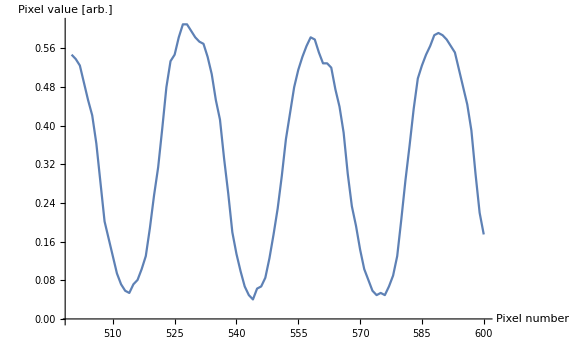

```mathematica
ListPlot[linedata[[500;;600]],Joined->True,LabelStyle->Directive[Black, Medium],AxesLabel-> {"Pixel number","Pixel value [arb.]"},ImageSize->Large]
```

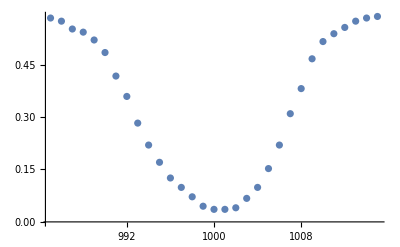

```mathematica
ListPlot[linedata[[985;;1015]]]
```

```mathematica
model = A (1-   Exp[(-((x-μx)^2+(y-μy)^2))/σ^2])
fit =FindFit[site,model,{μx,μy,σ,A},{x,y}]
```

```mathematica
model = A (1-   Exp[(-2(x-μ)^2)/σ^2]);
fit =FindFit[linedata[[979;;1021]],model,{{μ,1000},σ,A, {b,0.5}},x]
Show[Plot[model/.fit,{x,985,1015}],ListPlot[linedata[[985;;1015]]],AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Medium]
pixel = 1.12; (*μm*)
StringForm["real space waist `` [μm]",Values[fit[[2]]]*pixel]
```

{μ→999.981,σ→10.6518,A→0.561076,b→0.5}

real space waist 11.93 [μm]

## 805nm 3W laser

```mathematica
imagedir="trap_array_images\\";
AppendTo[$Path, FileNameJoin[{NotebookDirectory[],imagedir}]];
```

```mathematica
(*imagedir="../trap_array_images/";
SetDirectory[imagedir+NotebookDirectory[]];*)
img = ColorConvert[Import["array_more_closed_20200825.jpg"],"grayscale"]
```

-Graphics-

```mathematica
Show[ImageRotate[img,-0.01], ImageSize-> Medium]
```

-Graphics-

```mathematica
data = ImageData[ImageRotate[img,-0.01]];
data = data-data[[50,50]];(*subtract off the background*)
data = Replace[data,_?Negative-> 0,{2}]; 
data = data/Max[data]; 
lenx = data//Length;
leny= data[[1]]//Length;
```

```mathematica
Show[Image[data],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{860,1},{880,lenx}]}],ImageSize->Medium]
```

-Graphics-

```mathematica
Image[data[[860;;861, 1;; leny]]]
```

-Graphics-

```mathematica
Image[data[[869;;870,1;;leny]]]
```

-Graphics-

0.0627451

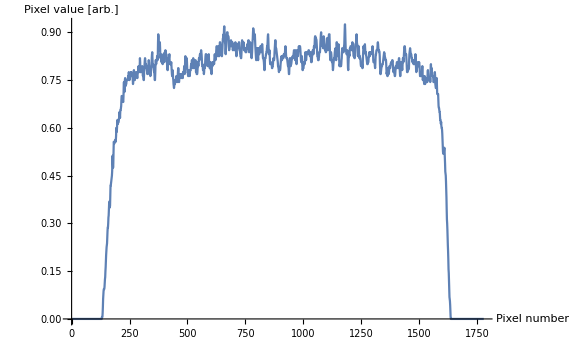

```mathematica
linedata = Transpose@{Range[leny],data[[860;;861,1;;leny]][[1]]};
ListPlot[linedata, Joined->True,AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Large]
```

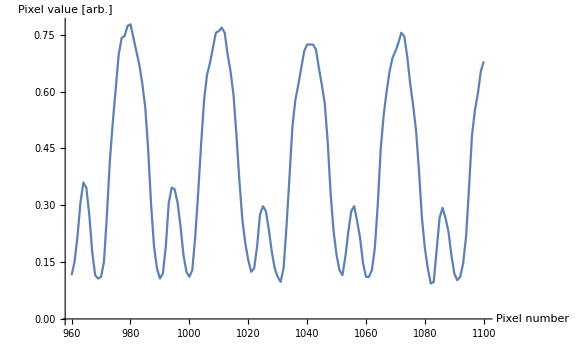

```mathematica
ListPlot[linedata[[960;;1100]],Joined->True,LabelStyle->Directive[Black, Medium],AxesLabel-> {"Pixel number","Pixel value [arb.]"},ImageSize->Large]
```

```mathematica
ListPlot[linedata[[500;;600]],Joined->True,LabelStyle->Directive[Black, Medium],AxesLabel-> {"Pixel number","Pixel value [arb.]"},ImageSize->Large]
```

-Graphics-

```mathematica
ListPlot[linedata[[985;;1015]]]
```

-Graphics-

```mathematica
model = A (1-   Exp[(-2(x-μ)^2)/σ^2]);
fit =FindFit[linedata[[979;;1021]],model,{{μ,1000},σ,A, {b,0.5}},x]
Show[Plot[model/.fit,{x,985,1015}],ListPlot[linedata[[985;;1015]]],AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Medium]
pixel = 1.12; (*μm*)
StringForm["real space waist `` [μm]",Values[fit[[2]]]*pixel]
```

{μ→999.981,σ→10.6518,A→0.561076,b→0.5}

real space waist 11.93 [μm]

```mathematica
Values[fit[[2]]]
```

6.01289

real space waist 1.12 (σ→6.01289) [μm]

```mathematica
sigma = 8.335; pixsize = 4/1750//N
```

0.00228571

1.7 um per pixel,

```mathematica
8*2.3
```

18.4

```mathematica
14 um
```

```mathematica
0.56/ⅇ^2//N
```

0.0757878

## before 2021/11

For a dark spot array, let P be the total power incident on the array mask. 
Mark says It = Id, so It = P_unit/d^2;

```mathematica
d = .430;(*array period, input plane*)
a = .100; (*array spot radius*)
illum = (20/35)^2;(*fraction of the array mask illuminated*)
A =14.8^2(* π 12^2*); (*the area of a 25.4mm disk optic*)
A = A*illum*chopped;
M = 1/100;(*array magnification*)
It=P/A;
```

```mathematica
It*10^-6(1/M)^2/.P-> 20(*site peak intensity in W/μm^2*)
```

0.00559259

```mathematica
kB = 1.38*^-23;
c=2.998*^8;
ϵ0 = 8.85*^-12;
λ = 8.52*^-7;
ω0 = 2π c/λ;
ℏ= 1.05*10^-34;
Γ = 2π 5.2227*10^6; (*Cesium D2 line*)
Δ= 2π(c/(8.05*^-7)-c/λ);
Udip = (3 π c^2 Γ)/(2 ω0^3 Δ);(*dipole trap potential seen by atom in units intensity*)
```

```mathematica
T/(2/(3 kB)Udip)10^-12/.T-> .0005(*intensity in W/m^2 reqd for desired trap depth*)
```

0.00103884

```mathematica
2/(3kB)Udip*It/.P->1.5
```

3.296×10^-15

Trent: 121 ~2x2 um sites, 500 mW--> site intensity is ~ 1mW/um

```mathematica
.5/(121)
```

```mathematica
0.004132231404958678
```

```mathematica
Clear[P]
```

```mathematica
Solve[P/(A 10^6)(1/M)^2==1,P]
```

{{P→21904.}}

```mathematica
A*10^6 M^2.001(*required power in W*)
```

21.904

```mathematica
500
```

### estimates

2021.11.2

```mathematica
xsites = 12;
d = 4.3*^-6;
P = 20;
A = xsites^2 d^2;
contrast=.8;

kB = 1.38*^-23;
c=2.998*^8;
ϵ0 = 8.85*^-12;
λD2 = 8.52*^-7;
λtrap = 8.08*^-7;
ω0 = 2π c/λD2;
ℏ= 1.05*10^-34;
Γ = 2π 5.2227*10^6; (*Cesium D2 line*)
IsEff =1.6536*(10^-3)/(0.1)^2;(*far detuned Is, W/m^2*) 
Δ= 2π(c/λtrap-c/λD2);
(*approx*)
Udip = (3 π c^2 Γ)/(2 ω0^3 Δ)*P/((1+xsites)^2*d^2)contrast;
(*better approx.. giving incorrect result?*)
Int = P/A;
(*Udip = (ℏ Δ)/2 Log[1+(contrast Int/IsEff)/(1+4(Δ^2/Γ^2))];*)
"Trap depth in mK"
10^3 Udip/kB
```

Trap depth in mK

3.9634

```mathematica
(12*4.3)^2-12^2
```

2518.56

```mathematica
(ℏ 2π *73*10^6)/kB
```

0.0034899

```mathematica
23^2*(π(23/2)^2)/23^2//N
```

415.476